## Initialization

```mathematica
Unprotect["Global`*"]
Clear["Global`*"]
ClearAll["Global`*"] 
Remove["Global`*"] 
<<Notation`
Off[Symbolize::bsymbexs]
Off[Remove::rmnsm]
AutoCollapse[]:=(If[$FrontEnd=!=$Failed,SelectionMove[EvaluationNotebook[],All,GeneratedCell];
FrontEndTokenExecute["SelectionCloseUnselectedCells"]])
Print["Variable Cleared"]
AutoCollapse[]
```

{}

Remove::rmnsm: There are no symbols matching "Global`*".

Variable Cleared

```mathematica
Symbolize[Subscript[u, ρ]]; Symbolize[Subscript[u, ϕ]]; Symbolize[Subscript[u, ζ]]; 
Symbolize[Subscript[u, a]^ρ];Symbolize[Subscript[u, a]^ϕ];Symbolize[Subscript[u, a]^ζ];
Symbolize[Subscript[u, b]^ρ];Symbolize[Subscript[u, b]^ϕ];Symbolize[Subscript[u, b]^ζ];
Symbolize[u^ρ]; Symbolize[u^ϕ]; Symbolize[u^ζ];
Symbolize[w^ρ]; Symbolize[w^ϕ]; Symbolize[w^ζ];
Symbolize[Subscript[w, ρ]]; Symbolize[Subscript[w, ϕ]]; Symbolize[Subscript[w, ζ]];
 Symbolize[N^𝔄]Symbolize[N^𝔅]Symbolize[N^ℭ];Symbolize[N^𝔇]Symbolize[N^𝔈]Symbolize[N^𝔉];
Symbolize[(U⃗)_n];Symbolize[(X⃗)_r];Symbolize[(U⃗)^n];Symbolize[X⃗];Symbolize[τ^n];
Symbolize[Subscript[a, ρ,𝔄]];Symbolize[Subscript[a, ϕ,𝔅]];Symbolize[Subscript[a, ζ,ℭ]];
Symbolize[Subscript[b, ρ,𝔇]];Symbolize[Subscript[b, ϕ,𝔈]];Symbolize[Subscript[b, ζ,𝔉]]
Symbolize[L̄];
 Notation[g_(i_·j_·)   ⟺  CoVarMetricCoeffs[[i_,j_]]]
Notation[g^(i_·j_·)   ⟺  ContraVarMetricCoeffs[[i_,j_]]]
Notation[Γ_(i_·j_·)^(k_·)   ⟺  Γ[[i_,j_,k_]]]
Notation[w^(i_·)   ⟺  ContraVarDispW[[i_]]]
Notation[u^(i_·)   ⟺  ContraVarDispU[[i_]]]
Notation[u_(i_·)   ⟺  CoVarDispU[[i_]]]
Notation[x^(i_·)   ⟺  Coords[[i_]]]
Notation[w_(j_·)   ⟺  CoVarDispW[[j_]]]
Notation[u^(i_·)|_(j_·)  ⟺  CovariantDU1[i_,j_]]
Notation[u_(i_·)|_(j_·)  ⟺  CovariantDU2[i_,j_]]
Notation[w^(i_·)|_(j_·)  ⟺  CovariantDW1[i_,j_]]
Notation[w_(i_·)|_(j_·)  ⟺  CovariantDW2[i_,j_]]
Notation[γ_(i_·j_·)   ⟺  StrainCovariantU[[i_,j_]]]
Notation[ϵ_(i_·j_·)   ⟺  StrainCovariantW[[i_,j_]]]
Notation[𝔼^(i_·j_·k_·l_·)   ⟺  StiffnessContra[[i_,j_,k_,l_]]]
Notation[(∂u_)/(∂x_)   ⟺  D[u_,x_]]
Notation[τ^(i_·j_·)   ⟺  StressContra[[i_,j_]]]
Symbolize[x_^h];Symbolize[x_^e];
Symbolize[Subscript[U, 1]^n];Symbolize[Subscript[U, 2]^n];Symbolize[Subscript[U, 3]^n]
Symbolize[Subscript[U, n]^1];Symbolize[Subscript[U, n]^2];Symbolize[Subscript[U, n]^3]
Symbolize[Subscript[u, ρ]^h];Symbolize[Subscript[u, ϕ]^h];Symbolize[Subscript[u, ζ]^h]
Symbolize[Subscript[η, g]];Symbolize[Subscript[n, x_]];
Symbolize[N^(i_)];Symbolize[N_(,x_)^(i_)];Symbolize[Subscript[x_, i_]];Symbolize[(x⃗)^h];
Symbolize[(f⃗)_(e,a)]
Symbolize[(J^e)^-1];
Symbolize[x̲];
Print["New Symbols Defined"]
AutoCollapse[]
```

New Symbols Defined

```mathematica
<<HaneeshPackages`
PrntRls={Subscript[u, 1]-> Subscript[u,1],Subscript[u, 2]-> Subscript[u,2],Subscript[u, 3]-> Subscript[u,3],
Subscript[x, 1]-> Subscript[x,1],Subscript[x, 2]-> Subscript[x,2],Subscript[x, 3]-> Subscript[x,3],
u^ρ-> Superscript[u,ρ],u^ϕ-> Superscript[u,ϕ],u^ζ-> Superscript[u,ζ],
Subscript[u, ρ]-> Subscript[u,ρ],Subscript[u, ϕ]-> Subscript[u,ϕ],Subscript[u, ζ]-> Subscript[u,ζ],
N^𝔄-> Superscript[N,𝔄],N^𝔅-> Superscript[N,𝔅],N^ℭ-> Superscript[N,ℭ],
N^𝔇-> Superscript[N,𝔇],N^𝔈-> Superscript[N,𝔈],N^𝔉-> Superscript[N,𝔉],N^(a)-> Superscript[N,"(a)"],N^(b)-> Superscript[N,"(b)"],
Subscript[a, ρ, 𝔄]-> Subscript[a,ρ,𝔄],Subscript[a, ϕ, 𝔅]-> Subscript[a,ϕ,𝔅],Subscript[a, ζ, ℭ]-> Subscript[a,ζ,ℭ],
Subscript[b, ρ, 𝔇]-> Subscript[b,ρ,𝔇],Subscript[b, ϕ, 𝔈]-> Subscript[b,ϕ,𝔈],Subscript[b, ζ, 𝔉]-> Subscript[b,ζ,𝔉],N_(,ζ)^(a)->Subsuperscript[N,",ζ","(a)"],N_(,ρ)^(a)->Subsuperscript[N,",ρ","(a)"],N_(,ζ)^(b)->Subsuperscript[N,",ζ","(b)"],N_(,ρ)^(b)->Subsuperscript[N,",ρ","(b)"],
Subscript[w, ρ]-> Subscript[w,ρ],Subscript[w, ϕ]-> Subscript[w,ϕ],Subscript[w, ζ]-> Subscript[w,ζ],
L̄->Overscript[L,_],Subscript[ΔT, 0]-> Subscript[ΔT,0]
};
GenerateMonoSubSuperscriptRules[]:=Module[{body, ww,zz,xx,yy,Prules1,Prules2,scripts},
body=Join[Alphabet["Greek"],Alphabet[],ToUpperCase[Alphabet[]],ToUpperCase[Alphabet["Greek"]]];
scripts=Join[Table[ToString[i],{i,1,9}],List@ToString[ϕ],Map[ToString,Alphabet["Greek"]]];
xx=Flatten@Outer[StringJoin,Map[ToString,body],{"⎵Subscript⎵"},scripts];
xx=Map[Symbol,xx];
yy=Flatten@Outer[Subscript,body,scripts];
Prules1=Table[xx[[i]]->yy[[i]],{i,1,Length@xx}];
ww=Flatten@Outer[StringJoin,Map[ToString,body],{"⎵Superscript⎵"},scripts];
ww=Map[Symbol,ww];
zz=Flatten@Outer[Superscript,body,scripts];
Prules2=Table[ww[[i]]->zz[[i]],{i,1,Length@xx}];
Join[Prules1,Prules2]]
(*PrntRls=Join[PrntRls,GenerateMonoSubSuperscriptRules[]];*)
Pprint[expri_]:=Module[{expr=expri},
expr/.PrntRls//MatrixForm//pdConv
];
Pprint[expri_,title_]:=Module[{expr=expri},
(title=expr)/.PrntRls//MatrixForm//pdConv
];
Print["Print Subroutines Defined"]
AutoCollapse[]
```

Print Subroutines Defined

```mathematica
Subscript[u, ρ]::usage="Covariant component of the displacement in the g^ρ direction (symbol)";
Subscript[u, ϕ]::usage="Covariant component of the displacement in the g^ϕ direction ";
Subscript[u, ζ]::usage="Covariant component of the displacement in the g^ζ direction ";

λ::usage="Lame constant (double)";
μ::usage="Lame constant (double)";
Subscript[ρ, 0]::usage="inner radius (double)";
Subscript[ρ, 1]::usage="outer radius (double)";
Subscript[ζ, 0]::usage="curvilinear coordinate ζ's lower bound(double)";
Subscript[ζ, 1]::usage="curvilinear coordinate ζ's upper bound(double)";
αΔT::usage="α=Coefficient of thermal expansion; ΔT=Temperature change function";

Subscript[n, el]::usage="\tNumber of Finite Elements";
Subscript[n, np]::usage="Number of Finite Element Nodes";
Subscript[n, dof]::usage="Number of degrees of freedom per node";
Subscript[n, en]::usage="Number of nodes per finite element";
Subscript[n, eq]::usage="Total Number of Equations";
Subscript[n, guass]:: usage="Number of integration points";
(x⃗)^h::usage="{ρ_A, ζ_A} = (x⃗)^h⟦A⟧\n A = Global node number\n {ρ_A, ζ_A}= Nodal co-ordinates\n Dimensions[(x⃗)^h]= n_npX n_sd ";
Subscript[n, sd]::usage="Number of space dimensions";
(*Data Structure Arrays*)

SetUpIDArray::usage="Call as SetUpIDArray[]. Will return the ID array";
IEN::usage="IEN(a,e) = A\n\n\ta = Local Node Number\n\te = Element Number\n\tA = Global Node Number";
ID::usage="Dimensions[ID]={n_dof,n_np}\n  
ID[i,A]=Piecewise[{{P,, A∈η-η_g}, {0, A∈η-η_g_i}}]
";
<<NDSolve`FEM`
Guass = N@{{0.308642,{-√3/5,-√3/5}},{0.493827,{0.0,-√3/5}},{0.308642,{√3/5,-√3/5}},{0.493827,{-√3/5,0.0}},{0.790123,{0.0,0.0}},{0.493827,{√3/5,0.0}},{0.308642,{-√3/5,√3/5}},{0.493827,{0.0,√3/5}},{0.308642,{√3/5,√3/5}}};
(N^(1))[ξ_,η_]=1/4(1-ξ)(1-η)(-ξ-η-1);
(N^(2))[ξ_,η_]=1/4(1+ξ)(1-η)(ξ-η-1);
(N^(3))[ξ_,η_]=1/4(1+ξ)(1+η)(ξ+η-1);
(N^(4))[ξ_,η_]=1/4(1-ξ)(1+η)(-ξ+η-1);
(N^(5))[ξ_,η_]=1/2(1-ξ^2)(1-η);
(N^(6))[ξ_,η_]=1/2(1+ξ)(1-η^2);
(N^(7))[ξ_,η_]=1/2(1-ξ^2)(1+η);
(N^(8))[ξ_,η_]=1/2(1-ξ)(1-η^2);
(N_(,ξ)^(1))[ξ_,η_]=D[(N^(1))[ξ,η],ξ];
(N_(,η)^(1))[ξ_,η_]=D[(N^(1))[ξ,η],η];
(N_(,ξ)^(2))[ξ_,η_]=D[(N^(2))[ξ,η],ξ];
(N_(,η)^(2))[ξ_,η_]=D[(N^(2))[ξ,η],η];
(N_(,ξ)^(3))[ξ_,η_]=D[(N^(3))[ξ,η],ξ];
(N_(,η)^(3))[ξ_,η_]=D[(N^(3))[ξ,η],η];
(N_(,ξ)^(4))[ξ_,η_]=D[(N^(4))[ξ,η],ξ];
(N_(,η)^(4))[ξ_,η_]=D[(N^(4))[ξ,η],η];
(N_(,ξ)^(5))[ξ_,η_]=D[(N^(5))[ξ,η],ξ];
(N_(,η)^(5))[ξ_,η_]=D[(N^(5))[ξ,η],η];
(N_(,ξ)^(6))[ξ_,η_]=D[(N^(6))[ξ,η],ξ];
(N_(,η)^(6))[ξ_,η_]=D[(N^(6))[ξ,η],η];
(N_(,ξ)^(7))[ξ_,η_]=D[(N^(7))[ξ,η],ξ];
(N_(,η)^(7))[ξ_,η_]=D[(N^(7))[ξ,η],η];
(N_(,ξ)^(8))[ξ_,η_]=D[(N^(8))[ξ,η],ξ];
(N_(,η)^(8))[ξ_,η_]=D[(N^(8))[ξ,η],η];
Print["Nomenclature defined"]
AutoCollapse[]
```

Nomenclature defined

## Problem Formulations: Theory

```mathematica
Γ=Table[0,{i,1,3},{j,1,3},{k,1,3}];
Γ[[;;,;;,1]]={{0,0,0},{0,-ρ,0},{0,0,0}};
Γ[[;;,;;,2]]={{0,1/ρ,0},{1/ρ,0,0},{0,0,0}};
Γ[[;;,;;,3]]={{0,-(L̄)/ρ,0},{-(L̄)/ρ,0,0},{0,0,0}};
Print["Christoffel Symbols Defined"]
AutoCollapse[]
```

Christoffel Symbols Defined

```mathematica
CoVarMetricCoeffs={{1,0,0},{0,ρ^2+(L̄)^2,L̄},{0,L̄,1}};
ContraVarMetricCoeffs={{1,0,0},{0,1/ρ^2,-(L̄)/ρ^2},{0,-(L̄)/ρ^2,(ρ^2+(L̄)^2)/ρ^2}};

Print[Style["Covariant Metric Tensor: ",Orange]]
  Table[g_(i·j·),{i,1,3},{j,1,3}]//Pprint
Print[Style["Contravariant Metric Tensor: ",Orange]]
Table[g^(i·j·),{i,1,3},{j,1,3}]//Pprint

AutoCollapse[]
```

Covariant Metric Tensor:

(1 | 0 | 0
0 | (L̄)^2+ρ^2 | L̄
0 | L̄ | 1)

Contravariant Metric Tensor:

(1 | 0 | 0
0 | 1/ρ^2 | -(L̄)/ρ^2
0 | -(L̄)/ρ^2 | ((L̄)^2+ρ^2)/ρ^2)

```mathematica
Coords={ρ,ϕ,ζ};
ContraVarDispU={Subscript[a, ρ,𝔄](N^𝔄)[ρ,ζ],Subscript[a, ϕ,𝔅](N^𝔅)[ρ,ζ],Subscript[a, ζ,ℭ](N^ℭ)[ρ,ζ]}; 
ContraVarDispW={Subscript[b, ρ,𝔇](N^𝔇)[ρ,ζ],Subscript[b, ϕ,𝔈](N^𝔈)[ρ,ζ],Subscript[b, ζ,𝔉](N^𝔉)[ρ,ζ]}; 
CoVarDispU=Table[∑_(j=1)^3 (g_(i·j·)u^(j·)),{i,1,3}];
CoVarDispW=Table[∑_(j=1)^3 (g_(i·j·)w^(j·)),{i,1,3}];


Table[x^(i·),{i,1,3}]//Pprint
Table[u_(i·),{i,1,3}]//Pprint
Table[u^(i·),{i,1,3}]//Pprint
Table[w_(i·),{i,1,3}]//Pprint
Table[w^(i·),{i,1,3}]//Pprint
AutoCollapse[]
```

(ρ
ϕ
ζ)

(a_(ρ,𝔄) N^𝔄(ρ,ζ)
((L̄)^2+ρ^2) a_(ϕ,𝔅) N^𝔅(ρ,ζ)+L̄ a_(ζ,ℭ) N^ℭ(ρ,ζ)
L̄ a_(ϕ,𝔅) N^𝔅(ρ,ζ)+a_(ζ,ℭ) N^ℭ(ρ,ζ))

(a_(ρ,𝔄) N^𝔄(ρ,ζ)
a_(ϕ,𝔅) N^𝔅(ρ,ζ)
a_(ζ,ℭ) N^ℭ(ρ,ζ))

(b_(ρ,𝔇) N^𝔇(ρ,ζ)
((L̄)^2+ρ^2) b_(ϕ,𝔈) N^𝔈(ρ,ζ)+L̄ b_(ζ,𝔉) N^𝔉(ρ,ζ)
L̄ b_(ϕ,𝔈) N^𝔈(ρ,ζ)+b_(ζ,𝔉) N^𝔉(ρ,ζ))

(b_(ρ,𝔇) N^𝔇(ρ,ζ)
b_(ϕ,𝔈) N^𝔈(ρ,ζ)
b_(ζ,𝔉) N^𝔉(ρ,ζ))

```mathematica
CovariantDU2[i_,j_]:=((∂u_(i·))/(∂x^(j·))-∑_(k=1)^3 (u_(k·)Γ_(i·j·)^(k·)));
StrainCovariantU=Table[1/2((u_(i·)|_(j·))+(u_(j·)|_(i·))),{i,1,3},{j,1,3}];

CovariantDW2[i_,j_]:=((∂w_(i·))/(∂x^(j·))-∑_(k=1)^3 (w_(k·)Γ_(i·j·)^(k·)));
StrainCovariantW=Table[1/2((w_(i·)|_(j·))+(w_(j·)|_(i·))),{i,1,3},{j,1,3}];

Print["Strain Tensors"]
{FullSimplify@Table[γ_(i·j·),{i,1,3},{j,1,3}]//Pprint(*,Flatten@FullSimplify@Table[ϵ_(i·j·),{i,1,3},{j,1,3}]//Pprint*)}
AutoCollapse[]
```

Strain Tensors

{(a_(ρ,𝔄) (∂N^𝔄(ρ,ζ))/(∂ρ) | 1/2 (((L̄)^2+ρ^2) a_(ϕ,𝔅) (∂N^𝔅(ρ,ζ))/(∂ρ)+L̄ a_(ζ,ℭ) (∂N^ℭ(ρ,ζ))/(∂ρ)) | 1/2 (L̄ a_(ϕ,𝔅) (∂N^𝔅(ρ,ζ))/(∂ρ)+a_(ρ,𝔄) (∂N^𝔄(ρ,ζ))/(∂ζ)+a_(ζ,ℭ) (∂N^ℭ(ρ,ζ))/(∂ρ))
1/2 (((L̄)^2+ρ^2) a_(ϕ,𝔅) (∂N^𝔅(ρ,ζ))/(∂ρ)+L̄ a_(ζ,ℭ) (∂N^ℭ(ρ,ζ))/(∂ρ)) | ρ a_(ρ,𝔄) N^𝔄(ρ,ζ) | 1/2 (((L̄)^2+ρ^2) a_(ϕ,𝔅) (∂N^𝔅(ρ,ζ))/(∂ζ)+L̄ a_(ζ,ℭ) (∂N^ℭ(ρ,ζ))/(∂ζ))
1/2 (L̄ a_(ϕ,𝔅) (∂N^𝔅(ρ,ζ))/(∂ρ)+a_(ρ,𝔄) (∂N^𝔄(ρ,ζ))/(∂ζ)+a_(ζ,ℭ) (∂N^ℭ(ρ,ζ))/(∂ρ)) | 1/2 (((L̄)^2+ρ^2) a_(ϕ,𝔅) (∂N^𝔅(ρ,ζ))/(∂ζ)+L̄ a_(ζ,ℭ) (∂N^ℭ(ρ,ζ))/(∂ζ)) | L̄ a_(ϕ,𝔅) (∂N^𝔅(ρ,ζ))/(∂ζ)+a_(ζ,ℭ) (∂N^ℭ(ρ,ζ))/(∂ζ))}

```mathematica
Clear[StiffnessContra];
StiffnessContra=μ Table[g^(i·r·) g^(j·s·)+g^(i·s·) g^(j·r·)+λ/μ g^(i·j·)g^(r·s·),{i,1,3},{j,1,3},{r,1,3},{s,1,3}];
Print["Stiffness Defined"]
AutoCollapse[]
```

Stiffness Defined

```mathematica
StressContra=Table[∑_(r=1)^3 ∑_(s=1)^3 𝔼^(i·j·r·s·)(γ_(r·s·)-αΔT[ρ,ζ] g_(r·s·)),{i,1,3},{j,1,3}];
Print["Stress Defined"]
Print["Stress Tensors"]
{FullSimplify@Table[τ^(i·j·),{i,1,3},{j,1,3}]//Pprint}
AutoCollapse[]
```

Stress Defined

Stress Tensors

{((λ a_(ρ,𝔄) N^𝔄(ρ,ζ)+ρ ((λ+2 μ) a_(ρ,𝔄) (∂N^𝔄(ρ,ζ))/(∂ρ)+λ a_(ζ,ℭ) (∂N^ℭ(ρ,ζ))/(∂ζ)-(3 λ+2 μ) αΔT(ρ,ζ)))/ρ | μ a_(ϕ,𝔅) (∂N^𝔅(ρ,ζ))/(∂ρ)-(μ L̄ a_(ρ,𝔄) (∂N^𝔄(ρ,ζ))/(∂ζ))/ρ^2 | (μ ((L̄)^2+ρ^2) a_(ρ,𝔄) (∂N^𝔄(ρ,ζ))/(∂ζ))/ρ^2+μ a_(ζ,ℭ) (∂N^ℭ(ρ,ζ))/(∂ρ)
μ a_(ϕ,𝔅) (∂N^𝔅(ρ,ζ))/(∂ρ)-(μ L̄ a_(ρ,𝔄) (∂N^𝔄(ρ,ζ))/(∂ζ))/ρ^2 | (ρ (-2 μ L̄ a_(ϕ,𝔅) (∂N^𝔅(ρ,ζ))/(∂ζ)+λ a_(ρ,𝔄) (∂N^𝔄(ρ,ζ))/(∂ρ)+λ a_(ζ,ℭ) (∂N^ℭ(ρ,ζ))/(∂ζ)-(3 λ+2 μ) αΔT(ρ,ζ))+(λ+2 μ) a_(ρ,𝔄) N^𝔄(ρ,ζ))/ρ^3 | (ρ (-L̄ (λ a_(ρ,𝔄) (∂N^𝔄(ρ,ζ))/(∂ρ)+(λ+μ) a_(ζ,ℭ) (∂N^ℭ(ρ,ζ))/(∂ζ))+μ ((L̄)^2+ρ^2) a_(ϕ,𝔅) (∂N^𝔅(ρ,ζ))/(∂ζ)+L̄ (3 λ+2 μ) αΔT(ρ,ζ))-L̄ (λ+2 μ) a_(ρ,𝔄) N^𝔄(ρ,ζ))/ρ^3
(μ ((L̄)^2+ρ^2) a_(ρ,𝔄) (∂N^𝔄(ρ,ζ))/(∂ζ))/ρ^2+μ a_(ζ,ℭ) (∂N^ℭ(ρ,ζ))/(∂ρ) | (ρ (-L̄ (λ a_(ρ,𝔄) (∂N^𝔄(ρ,ζ))/(∂ρ)+(λ+μ) a_(ζ,ℭ) (∂N^ℭ(ρ,ζ))/(∂ζ))+μ ((L̄)^2+ρ^2) a_(ϕ,𝔅) (∂N^𝔅(ρ,ζ))/(∂ζ)+L̄ (3 λ+2 μ) αΔT(ρ,ζ))-L̄ (λ+2 μ) a_(ρ,𝔄) N^𝔄(ρ,ζ))/ρ^3 | (a_(ρ,𝔄) ((L̄)^2 (λ+2 μ)+λ ρ^2) N^𝔄(ρ,ζ)-ρ ((L̄)^2+ρ^2) (-λ a_(ρ,𝔄) (∂N^𝔄(ρ,ζ))/(∂ρ)-(λ+2 μ) a_(ζ,ℭ) (∂N^ℭ(ρ,ζ))/(∂ζ)+(3 λ+2 μ) αΔT(ρ,ζ)))/ρ^3)}

```mathematica
W=FullSimplify@Sum[τ^(i·j·)ϵ_(i·j·),{i,1,3},{j,1,3}];
Print["Strain Energy Density"]
AutoCollapse[]
```

Strain Energy Density

```mathematica
Subscript[W, el] = FullSimplify@Sum[1/2 τ^(i·j·)(ϵ_(i·j·)-αΔT[ρ,ζ] g_(i·j·)),{i,1,3},{j,1,3}];
```

```mathematica
Patt={
 x_[ρ,ζ] Derivative[0,1][(y_)][ρ,ζ],
x_[ρ,ζ] Derivative[1,0][(y_)][ρ,ζ],Derivative[1,0][(x_)][ρ,ζ]Derivative[1,0][(y_)][ρ,ζ],
Derivative[0,1][(x_)][ρ,ζ]Derivative[0,1][(y_)][ρ,ζ],
Derivative[0,1][(x_)][ρ,ζ]Derivative[1,0][(y_)][ρ,ζ]
x_[ρ,ζ] y_[ρ,ζ]};

Print[Style["Global Stiffness Matrix",Orange]]
K=Simplify@Outer[D[W ,#1,#2]&,{Subscript[a, ρ,𝔄],Subscript[a, ϕ,𝔅],Subscript[a, ζ,ℭ]},{Subscript[b, ρ,𝔇],Subscript[b, ϕ,𝔈],Subscript[b, ζ,𝔉]}];
Flatten@Table[Collect[Expand@K[[i,j]],Patt,Simplify],{i,1,3},{j,1,3}]//Pprint
AutoCollapse[]
```

Global Stiffness Matrix

(((μ (L̄)^2)/ρ^2+μ) (∂N^𝔄(ρ,ζ))/(∂ζ) (∂N^𝔇(ρ,ζ))/(∂ζ)+((λ+2 μ) N^𝔄(ρ,ζ) N^𝔇(ρ,ζ))/ρ^2+(λ+2 μ) (∂N^𝔄(ρ,ζ))/(∂ρ) (∂N^𝔇(ρ,ζ))/(∂ρ)+(λ N^𝔄(ρ,ζ) (∂N^𝔇(ρ,ζ))/(∂ρ))/ρ+(λ N^𝔇(ρ,ζ) (∂N^𝔄(ρ,ζ))/(∂ρ))/ρ
-(2 μ L̄ N^𝔄(ρ,ζ) (∂N^𝔈(ρ,ζ))/(∂ζ))/ρ
λ (∂N^𝔄(ρ,ζ))/(∂ρ) (∂N^𝔉(ρ,ζ))/(∂ζ)+(λ N^𝔄(ρ,ζ) (∂N^𝔉(ρ,ζ))/(∂ζ))/ρ+μ (∂N^𝔄(ρ,ζ))/(∂ζ) (∂N^𝔉(ρ,ζ))/(∂ρ)
-(2 μ L̄ N^𝔇(ρ,ζ) (∂N^𝔅(ρ,ζ))/(∂ζ))/ρ
(μ ((L̄)^2+ρ^2)^2 (∂N^𝔅(ρ,ζ))/(∂ζ) (∂N^𝔈(ρ,ζ))/(∂ζ))/ρ^2+μ ((L̄)^2+ρ^2) (∂N^𝔅(ρ,ζ))/(∂ρ) (∂N^𝔈(ρ,ζ))/(∂ρ)
((μ (L̄)^3)/ρ^2+μ L̄) (∂N^𝔅(ρ,ζ))/(∂ζ) (∂N^𝔉(ρ,ζ))/(∂ζ)+μ L̄ (∂N^𝔅(ρ,ζ))/(∂ρ) (∂N^𝔉(ρ,ζ))/(∂ρ)
λ (∂N^ℭ(ρ,ζ))/(∂ζ) (∂N^𝔇(ρ,ζ))/(∂ρ)+(λ N^𝔇(ρ,ζ) (∂N^ℭ(ρ,ζ))/(∂ζ))/ρ+μ (∂N^ℭ(ρ,ζ))/(∂ρ) (∂N^𝔇(ρ,ζ))/(∂ζ)
((μ (L̄)^3)/ρ^2+μ L̄) (∂N^ℭ(ρ,ζ))/(∂ζ) (∂N^𝔈(ρ,ζ))/(∂ζ)+μ L̄ (∂N^ℭ(ρ,ζ))/(∂ρ) (∂N^𝔈(ρ,ζ))/(∂ρ)
(μ ((L̄)^2/ρ^2+2)+λ) (∂N^ℭ(ρ,ζ))/(∂ζ) (∂N^𝔉(ρ,ζ))/(∂ζ)+μ (∂N^ℭ(ρ,ζ))/(∂ρ) (∂N^𝔉(ρ,ζ))/(∂ρ))

```mathematica
F=Simplify@Map[D[(-W /.{Subscript[a, ρ,𝔄]->0,Subscript[a, ϕ,𝔅]->0,Subscript[a, ζ,ℭ]->0}),#]&,{Subscript[b, ρ,𝔇],Subscript[b, ϕ,𝔈],Subscript[b, ζ,𝔉]}];
Print[Style["Global Force Matrix",Orange]]
Flatten@Table[Collect[Expand@F[[i]],Patt,Simplify],{i,1,3}]//Pprint
AutoCollapse[]
```

Global Force Matrix

(((3 λ+2 μ) αΔT(ρ,ζ) N^𝔇(ρ,ζ))/ρ+(3 λ+2 μ) αΔT(ρ,ζ) (∂N^𝔇(ρ,ζ))/(∂ρ)
0
(3 λ+2 μ) αΔT(ρ,ζ) (∂N^𝔉(ρ,ζ))/(∂ζ))

Global to Local Transformation

```mathematica
K/.((Derivative[0,1][(N^𝔄)])[ρ,ζ] | (Derivative[0,1][(N^𝔅)])[ρ,ζ] | (Derivative[0,1][(N^ℭ)])[ρ,ζ])-> (N_(,ζ)^(a))[ξ,η]/.((Derivative[1,0][(N^𝔄)])[ρ,ζ] | (Derivative[1,0][(N^𝔅)])[ρ,ζ] | (Derivative[1,0][(N^ℭ)])[ρ,ζ])-> (N_(,ρ)^(a))[ξ,η]/.((N^𝔄)[ρ,ζ]| (N^𝔅)[ρ,ζ] | (N^ℭ)[ρ,ζ])->(N^(a))[ξ,η]/.((Derivative[0,1][(N^𝔇)])[ρ,ζ]| (Derivative[0,1][(N^𝔈)])[ρ,ζ] | (Derivative[0,1][(N^𝔉)])[ρ,ζ])-> (N_(,ζ)^(b))[ξ,η]/.((Derivative[1,0][(N^𝔇)])[ρ,ζ]| (Derivative[1,0][(N^𝔈)])[ρ,ζ] | (Derivative[1,0][(N^𝔉)])[ρ,ζ])-> (N_(,ρ)^(b))[ξ,η]/.((N^𝔇)[ρ,ζ]| (N^𝔈)[ρ,ζ] | (N^𝔉)[ρ,ζ])->(N^(b))[ξ,η]
AutoCollapse[]
```

{{1/ρ^2(μ ((L̄)^2+ρ^2) N_(,ζ)^(a)[ξ,η] N_(,ζ)^(b)[ξ,η]+ρ N_(,ρ)^(a)[ξ,η] ((λ+2 μ) ρ N_(,ρ)^(b)[ξ,η]+λ N^(b)[ξ,η])+N^(a)[ξ,η] (λ ρ N_(,ρ)^(b)[ξ,η]+(λ+2 μ) N^(b)[ξ,η])),-(2 L̄ μ N_(,ζ)^(b)[ξ,η] N^(a)[ξ,η])/ρ,λ N_(,ζ)^(b)[ξ,η] N_(,ρ)^(a)[ξ,η]+μ N_(,ζ)^(a)[ξ,η] N_(,ρ)^(b)[ξ,η]+(λ N_(,ζ)^(b)[ξ,η] N^(a)[ξ,η])/ρ},{-(2 L̄ μ N_(,ζ)^(a)[ξ,η] N^(b)[ξ,η])/ρ,(μ ((L̄)^2+ρ^2) (((L̄)^2+ρ^2) N_(,ζ)^(a)[ξ,η] N_(,ζ)^(b)[ξ,η]+ρ^2 N_(,ρ)^(a)[ξ,η] N_(,ρ)^(b)[ξ,η]))/ρ^2,(L̄ μ (((L̄)^2+ρ^2) N_(,ζ)^(a)[ξ,η] N_(,ζ)^(b)[ξ,η]+ρ^2 N_(,ρ)^(a)[ξ,η] N_(,ρ)^(b)[ξ,η]))/ρ^2},{μ N_(,ζ)^(b)[ξ,η] N_(,ρ)^(a)[ξ,η]+λ N_(,ζ)^(a)[ξ,η] N_(,ρ)^(b)[ξ,η]+(λ N_(,ζ)^(a)[ξ,η] N^(b)[ξ,η])/ρ,(L̄ μ (((L̄)^2+ρ^2) N_(,ζ)^(a)[ξ,η] N_(,ζ)^(b)[ξ,η]+ρ^2 N_(,ρ)^(a)[ξ,η] N_(,ρ)^(b)[ξ,η]))/ρ^2,(((L̄)^2 μ+(λ+2 μ) ρ^2) N_(,ζ)^(a)[ξ,η] N_(,ζ)^(b)[ξ,η]+μ ρ^2 N_(,ρ)^(a)[ξ,η] N_(,ρ)^(b)[ξ,η])/ρ^2}}

```mathematica
F/.((Derivative[0,1][(N^𝔄)])[ρ,ζ] | (Derivative[0,1][(N^𝔅)])[ρ,ζ] | (Derivative[0,1][(N^ℭ)])[ρ,ζ])-> (N_(,ζ)^(a))[ξ,η]/.((Derivative[1,0][(N^𝔄)])[ρ,ζ] | (Derivative[1,0][(N^𝔅)])[ρ,ζ] | (Derivative[1,0][(N^ℭ)])[ρ,ζ])-> (N_(,ρ)^(a))[ξ,η]/.((N^𝔄)[ρ,ζ]| (N^𝔅)[ρ,ζ] | (N^ℭ)[ρ,ζ])->(N^(a))[ξ,η]/.((Derivative[0,1][(N^𝔇)])[ρ,ζ]| (Derivative[0,1][(N^𝔈)])[ρ,ζ] | (Derivative[0,1][(N^𝔉)])[ρ,ζ])-> (N_(,ζ)^(b))[ξ,η]/.((Derivative[1,0][(N^𝔇)])[ρ,ζ]| (Derivative[1,0][(N^𝔈)])[ρ,ζ] | (Derivative[1,0][(N^𝔉)])[ρ,ζ])-> (N_(,ρ)^(b))[ξ,η]/.((N^𝔇)[ρ,ζ]| (N^𝔈)[ρ,ζ] | (N^𝔉)[ρ,ζ])->(N^(b))[ξ,η]
AutoCollapse[]
```

{((3 λ+2 μ) (ρ N_(,ρ)^(b)[ξ,η]+N^(b)[ξ,η]) αΔT[ρ,ζ])/ρ,0,(3 λ+2 μ) N_(,ζ)^(b)[ξ,η] αΔT[ρ,ζ]}

```mathematica
Subscript[W, el]/.((Derivative[0,1][(N^𝔄)])[ρ,ζ] | (Derivative[0,1][(N^𝔅)])[ρ,ζ] | (Derivative[0,1][(N^ℭ)])[ρ,ζ])-> (N_(,ζ)^(a))[ξ,η]/.((Derivative[1,0][(N^𝔄)])[ρ,ζ] | (Derivative[1,0][(N^𝔅)])[ρ,ζ] | (Derivative[1,0][(N^ℭ)])[ρ,ζ])-> (N_(,ρ)^(a))[ξ,η]/.((N^𝔄)[ρ,ζ]| (N^𝔅)[ρ,ζ] | (N^ℭ)[ρ,ζ])->(N^(a))[ξ,η]/.((Derivative[0,1][(N^𝔇)])[ρ,ζ]| (Derivative[0,1][(N^𝔈)])[ρ,ζ] | (Derivative[0,1][(N^𝔉)])[ρ,ζ])-> (N_(,ζ)^(b))[ξ,η]/.((Derivative[1,0][(N^𝔇)])[ρ,ζ]| (Derivative[1,0][(N^𝔈)])[ρ,ζ] | (Derivative[1,0][(N^𝔉)])[ρ,ζ])-> (N_(,ρ)^(b))[ξ,η]/.((N^𝔇)[ρ,ζ]| (N^𝔈)[ρ,ζ] | (N^𝔉)[ρ,ζ])->(N^(b))[ξ,η]/.Subscript[a, ρ,𝔄]-> Subscript[u, a]^ρ/.Subscript[a, ϕ,𝔅]-> Subscript[u, a]^ϕ/.Subscript[a, ζ,ℭ]-> Subscript[u, a]^ζ/.Subscript[b, ρ,𝔇]-> Subscript[u, b]^ρ/.Subscript[b, ϕ,𝔈]-> Subscript[u, b]^ϕ/.Subscript[b, ζ,𝔉]-> Subscript[u, b]^ζ// FullSimplify
```

1/(2 ρ^2)(u_a^ρ u_b^ρ λ ρ^2 N_(,ρ)^(a)[ξ,η] N_(,ρ)^(b)[ξ,η]+u_a^ζ u_b^ζ μ ρ^2 N_(,ρ)^(a)[ξ,η] N_(,ρ)^(b)[ξ,η]+L̄ u_a^ϕ u_b^ζ μ ρ^2 N_(,ρ)^(a)[ξ,η] N_(,ρ)^(b)[ξ,η]+2 u_a^ρ u_b^ρ μ ρ^2 N_(,ρ)^(a)[ξ,η] N_(,ρ)^(b)[ξ,η]+L̄ u_a^ζ u_b^ϕ μ ρ^2 N_(,ρ)^(a)[ξ,η] N_(,ρ)^(b)[ξ,η]+(L̄)^2 u_a^ϕ u_b^ϕ μ ρ^2 N_(,ρ)^(a)[ξ,η] N_(,ρ)^(b)[ξ,η]+u_a^ϕ u_b^ϕ μ ρ^4 N_(,ρ)^(a)[ξ,η] N_(,ρ)^(b)[ξ,η]+u_a^ρ u_b^ρ λ ρ N_(,ρ)^(b)[ξ,η] N^(a)[ξ,η]+u_a^ρ u_b^ρ λ ρ N_(,ρ)^(a)[ξ,η] N^(b)[ξ,η]+u_a^ρ u_b^ρ λ N^(a)[ξ,η] N^(b)[ξ,η]+2 u_a^ρ u_b^ρ μ N^(a)[ξ,η] N^(b)[ξ,η]-(3 λ+2 μ) ρ (u_a^ρ ρ N_(,ρ)^(a)[ξ,η]+u_b^ρ ρ N_(,ρ)^(b)[ξ,η]+u_a^ρ N^(a)[ξ,η]+u_b^ρ N^(b)[ξ,η]) αΔT[ρ,ζ]+3 (3 λ+2 μ) ρ^2 αΔT[ρ,ζ]^2+ρ N_(,ζ)^(b)[ξ,η] ((u_a^ρ u_b^ζ λ+u_a^ζ u_b^ρ μ) ρ N_(,ρ)^(a)[ξ,η]+u_a^ρ (u_b^ζ λ-2 L̄ u_b^ϕ μ) N^(a)[ξ,η]-u_b^ζ (3 λ+2 μ) ρ αΔT[ρ,ζ])+N_(,ζ)^(a)[ξ,η] (((L̄)^2 (u_a^ρ u_b^ρ+(u_a^ζ+L̄ u_a^ϕ) (u_b^ζ+L̄ u_b^ϕ)) μ+(u_a^ζ u_b^ζ λ+(2 u_a^ζ u_b^ζ+L̄ u_a^ϕ u_b^ζ+u_a^ρ u_b^ρ+L̄ (u_a^ζ+2 L̄ u_a^ϕ) u_b^ϕ) μ) ρ^2+u_a^ϕ u_b^ϕ μ ρ^4) N_(,ζ)^(b)[ξ,η]+ρ ((u_a^ζ u_b^ρ λ+u_a^ρ u_b^ζ μ) ρ N_(,ρ)^(b)[ξ,η]+u_b^ρ (u_a^ζ λ-2 L̄ u_a^ϕ μ) N^(b)[ξ,η]-u_a^ζ (3 λ+2 μ) ρ αΔT[ρ,ζ])))

## Problem Solution: Numerics

### Numerics subroutine:

```mathematica
Subscript[SetUpη, g][Coordinates0_,tol_:0.0001]:=Module[{Coordinates=Coordinates0,Subscript[n, np], Subscript[ρ, i],Subscript[ζ, i],Subscript[η, g]},
Subscript[n, np]=Length@Coordinates;
Subscript[η, g]={{},{},{}};
For[i=1,i≤Subscript[n, np],i++,
{Subscript[ρ, i],Subscript[ζ, i]}=Coordinates[[i]];
If[Abs[Subscript[ζ, i]-Subscript[ζ, 0]]≤   tol,AppendTo[Subscript[η, g][[2]],i]; AppendTo[Subscript[η, g][[3]],i]];
];
Subscript[η, g] 
]
```

```mathematica
SetUpIDArray[]:=Module[{P,A,i,ID},
ID=Table[0,{i,1,Subscript[n, dof]},{j,1,Subscript[n, np]}];
P=1;
For[A=1,A≤ Subscript[n, np],A++,
For[i=1,i≤ Subscript[n, dof],i++,
If[!MemberQ[Subscript[η, g][[i]],A],ID[[i,A]]=P;P=P+1,ID[[i,A]]=0];
];
];
ID
]
```

```mathematica
(k^e)[{ξ_,η_},{ρ_,ζ_}]:={{1/ρ^2(μ ((L̄)^2+ρ^2) (N_(,ζ)^(a))[ξ,η] (N_(,ζ)^(b))[ξ,η]+ρ (N_(,ρ)^(a))[ξ,η] ((λ+2 μ) ρ (N_(,ρ)^(b))[ξ,η]+λ (N^(b))[ξ,η])+(N^(a))[ξ,η] (λ ρ (N_(,ρ)^(b))[ξ,η]+(λ+2 μ) (N^(b))[ξ,η])),-(2 L̄ μ (N_(,ζ)^(b))[ξ,η] (N^(a))[ξ,η])/ρ,λ (N_(,ζ)^(b))[ξ,η] (N_(,ρ)^(a))[ξ,η]+μ (N_(,ζ)^(a))[ξ,η] (N_(,ρ)^(b))[ξ,η]+(λ (N_(,ζ)^(b))[ξ,η] (N^(a))[ξ,η])/ρ},{-(2 L̄ μ (N_(,ζ)^(a))[ξ,η] (N^(b))[ξ,η])/ρ,(μ ((L̄)^2+ρ^2) (((L̄)^2+ρ^2) (N_(,ζ)^(a))[ξ,η] (N_(,ζ)^(b))[ξ,η]+ρ^2 (N_(,ρ)^(a))[ξ,η] (N_(,ρ)^(b))[ξ,η]))/ρ^2,(L̄ μ (((L̄)^2+ρ^2) (N_(,ζ)^(a))[ξ,η] (N_(,ζ)^(b))[ξ,η]+ρ^2 (N_(,ρ)^(a))[ξ,η] (N_(,ρ)^(b))[ξ,η]))/ρ^2},{μ (N_(,ζ)^(b))[ξ,η] (N_(,ρ)^(a))[ξ,η]+λ (N_(,ζ)^(a))[ξ,η] (N_(,ρ)^(b))[ξ,η]+(λ (N_(,ζ)^(a))[ξ,η] (N^(b))[ξ,η])/ρ,(L̄ μ (((L̄)^2+ρ^2) (N_(,ζ)^(a))[ξ,η] (N_(,ζ)^(b))[ξ,η]+ρ^2 (N_(,ρ)^(a))[ξ,η] (N_(,ρ)^(b))[ξ,η]))/ρ^2,(((L̄)^2 μ+(λ+2 μ) ρ^2) (N_(,ζ)^(a))[ξ,η] (N_(,ζ)^(b))[ξ,η]+μ ρ^2 (N_(,ρ)^(a))[ξ,η] (N_(,ρ)^(b))[ξ,η])/ρ^2}}

(f^e)[{ξ_,η_},{ρ_,ζ_}]:={((3 λ+2 μ) (ρ (N_(,ρ)^(b))[ξ,η]+(N^(b))[ξ,η]) αΔT[ρ,ζ])/ρ,0,(3 λ+2 μ) (N_(,ζ)^(b))[ξ,η] αΔT[ρ,ζ]}
AutoCollapse[]
```

```mathematica
CalculateGuassPoints[e0_]:=Module[{e=e0,P,Q,R,S,T,U,V,W,Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4],Subscript[x, 5],Subscript[x, 6],Subscript[x, 7],Subscript[x, 8],Subscript[x, 9],Subscript[y, 1],Subscript[y, 2],Subscript[y, 3],Subscript[y, 4],Subscript[y, 5],Subscript[y, 6],Subscript[y, 7],Subscript[y, 8],Subscript[y, 9],GuassPointsSpatial,GuassPointsNatural,GuassWeights,i,Subscript[w, i],Subscript[ξ, i],Subscript[η, i],Subscript[ρ, i],Subscript[ζ, i]},
{P,Q,R,S,T,U,V,W}=IEN[[;;,e]];
{{Subscript[x, 1],Subscript[y, 1]},{Subscript[x, 2],Subscript[y, 2]},{Subscript[x, 3],Subscript[y, 3]},{Subscript[x, 4],Subscript[y, 4]},{Subscript[x, 5],Subscript[y, 5]},{Subscript[x, 6],Subscript[y, 6]},{Subscript[x, 7],Subscript[y, 7]},{Subscript[x, 8],Subscript[y, 8]}}=((x⃗)^h)[[{P,Q,R,S,T,U,V,W}]];
GuassWeights={};
GuassPointsSpatial={};
GuassPointsNatural={};
For[i=1,i≤ Subscript[n, guass],i++,
{Subscript[w, i],{Subscript[ξ, i],Subscript[η, i]}}=Guass[[i]];
{Subscript[ρ, i],Subscript[ζ, i]}={(N^(1))[Subscript[ξ, i],Subscript[η, i]] Subscript[x, 1]+(N^(2))[Subscript[ξ, i],Subscript[η, i]] Subscript[x, 2]+(N^(3))[Subscript[ξ, i],Subscript[η, i]] Subscript[x, 3]+(N^(4))[Subscript[ξ, i],Subscript[η, i]] Subscript[x, 4]+(N^(5))[Subscript[ξ, i],Subscript[η, i]] Subscript[x, 5]+(N^(6))[Subscript[ξ, i],Subscript[η, i]] Subscript[x, 6]+(N^(7))[Subscript[ξ, i],Subscript[η, i]] Subscript[x, 7]+(N^(8))[Subscript[ξ, i],Subscript[η, i]] Subscript[x, 8],
(N^(1))[Subscript[ξ, i],Subscript[η, i]] Subscript[y, 1]+(N^(2))[Subscript[ξ, i],Subscript[η, i]] Subscript[y, 2]+(N^(3))[Subscript[ξ, i],Subscript[η, i]] Subscript[y, 3]+(N^(4))[Subscript[ξ, i],Subscript[η, i]] Subscript[y, 4]+(N^(5))[Subscript[ξ, i],Subscript[η, i]] Subscript[y, 5]+(N^(6))[Subscript[ξ, i],Subscript[η, i]] Subscript[y, 6]+(N^(7))[Subscript[ξ, i],Subscript[η, i]] Subscript[y, 7]+(N^(8))[Subscript[ξ, i],Subscript[η, i]] Subscript[y, 8]};
AppendTo[GuassPointsSpatial,{Subscript[ρ, i],Subscript[ζ, i]}];
AppendTo[GuassPointsNatural,{Subscript[ξ, i],Subscript[η, i]}];
AppendTo[GuassWeights,Subscript[w, i]];
];
{GuassWeights,GuassPointsNatural,GuassPointsSpatial}
]
```

```mathematica
ElementJacobian[e0_]:=Module[{e=e0,P,Q,R,S,T,U,V,W,Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4],Subscript[x, 5],Subscript[x, 6],Subscript[x, 7],Subscript[x, 8],Subscript[x, 9],Subscript[y, 1],Subscript[y, 2],Subscript[y, 3],Subscript[y, 4],Subscript[y, 5],Subscript[y, 6],Subscript[y, 7],Subscript[y, 8],Subscript[y, 9],J^e,B^e,dNξ,dNη,J11,J12,J21,J22,detJ,InverseJ^e,deterJ},
{P,Q,R,S,T,U,V,W}=IEN[[;;,e]];
{{Subscript[x, 1],Subscript[y, 1]},{Subscript[x, 2],Subscript[y, 2]},{Subscript[x, 3],Subscript[y, 3]},{Subscript[x, 4],Subscript[y, 4]},{Subscript[x, 5],Subscript[y, 5]},{Subscript[x, 6],Subscript[y, 6]},{Subscript[x, 7],Subscript[y, 7]},{Subscript[x, 8],Subscript[y, 8]}}=((x⃗)^h)[[{P,Q,R,S,T,U,V,W}]];
dNξ[ξ_,η_] = {(N_(,ξ)^(1))[ξ,η],(N_(,ξ)^(2))[ξ,η],(N_(,ξ)^(3))[ξ,η],(N_(,ξ)^(4))[ξ,η],(N_(,ξ)^(5))[ξ,η],(N_(,ξ)^(6))[ξ,η],(N_(,ξ)^(7))[ξ,η],(N_(,ξ)^(8))[ξ,η]};
dNη[ξ_,η_] = {(N_(,η)^(1))[ξ,η],(N_(,η)^(2))[ξ,η],(N_(,η)^(3))[ξ,η],(N_(,η)^(4))[ξ,η],(N_(,η)^(5))[ξ,η],(N_(,η)^(6))[ξ,η],(N_(,η)^(7))[ξ,η],(N_(,η)^(8))[ξ,η]};
x = {Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4],Subscript[x, 5],Subscript[x, 6],Subscript[x, 7],Subscript[x, 8]};
y = {Subscript[y, 1],Subscript[y, 2],Subscript[y, 3],Subscript[y, 4],Subscript[y, 5],Subscript[y, 6],Subscript[y, 7],Subscript[y, 8]};
J11[ξ_,η_] = dNξ[ξ,η].x;
J12[ξ_,η_] = dNξ[ξ,η].y;
J21[ξ_,η_] = dNη[ξ,η].x;
J22[ξ_,η_] = dNη[ξ,η].y;
(J^e)[ξ_,η_]={{J11[ξ,η],J12[ξ,η]},{J21[ξ,η],J22[ξ,η]}};
detJ[ξ_,η_] = FullSimplify[(J11[ξ,η]*J22[ξ,η]-J12[ξ,η]*J21[ξ,η])];
deterJ = detJ[0,0];
(InverseJ^e)[ξ_,η_]= FullSimplify[1/detJ[ξ,η]{{J22[ξ,η],-J12[ξ,η]},{-J21[ξ,η],J11[ξ,η]}}];
(B^e)[ξ_,η_]= FullSimplify[(InverseJ^e)[ξ,η].{ {(N_(,ξ)^(1))[ξ,η],(N_(,ξ)^(2))[ξ,η],(N_(,ξ)^(3))[ξ,η],(N_(,ξ)^(4))[ξ,η],(N_(,ξ)^(5))[ξ,η],(N_(,ξ)^(6))[ξ,η],(N_(,ξ)^(7))[ξ,η],(N_(,ξ)^(8))[ξ,η]},{(N_(,η)^(1))[ξ,η],(N_(,η)^(2))[ξ,η],(N_(,η)^(3))[ξ,η],(N_(,η)^(4))[ξ,η],(N_(,η)^(5))[ξ,η],(N_(,η)^(6))[ξ,η],(N_(,η)^(7))[ξ,η],(N_(,η)^(8))[ξ,η]} }];
{deterJ,B^e}
]
```

```mathematica
GuassIntegrate[e0_Integer,f0_]:=Module[{e=e0,f=f0,Subscript[w, i],Subscript[ξ, i],Subscript[η, i],Subscript[ρ, i],Subscript[ζ, i],ℐ=0,GuassPoints},
GuassPoints=CalculateGuassPoints[e];
For[i=1,i≤ Subscript[n, guass],i++,
{Subscript[w, i],{Subscript[ξ, i],Subscript[η, i]},{Subscript[ρ, i],Subscript[ζ, i]}}=GuassPoints[[;;,i]];
ℐ+=Subscript[w, i] f[{Subscript[ξ, i],Subscript[η, i]},{Subscript[ρ, i],Subscript[ζ, i]}];
];
ℐ
]
```

```mathematica
ComputeElementStiffnessMatrix[e0_]:=Module[{e=e0,A,B,P,Q, 𝒾,𝒿,a,b,ρ,ζ,ξ,η,j^e,(J^e)^-1,B^e,ℐ=0.0,f},
{j^e,B^e}=ElementJacobian[e];
For[a=1,a≤ Subscript[n, en],a++,
For[b=1,b≤ Subscript[n, en],b++,
A=IEN[[a,e]];
B=IEN[[b,e]];
{(N_(,ρ)^(a))[ξ_,η_],(N_(,ζ)^(a))[ξ_,η_]}=(B^e)[ξ,η][[;;,a]];
{(N_(,ρ)^(b))[ξ_,η_],(N_(,ζ)^(b))[ξ_,η_]}=(B^e)[ξ,η][[;;,b]];
(N^(a))[ξ_,η_]=NMat[ξ,η][[a]];
(N^(b))[ξ_,η_]=NMat[ξ,η][[b]];
For[𝒾=1,𝒾≤ Subscript[n, dof],𝒾++,
For[𝒿=1,𝒿≤ Subscript[n, dof],𝒿++,
f[{ξ_,η_},{ρ_,ζ_}]=j^e(k^e)[{ξ,η},{ρ,ζ}][[𝒾,𝒿]]ρ;
ℐ=GuassIntegrate[e,f];
P=ID[[𝒾,A]];Q=ID[[𝒿,B]];
If[P≠0 && Q≠ 0,KMat[[P,Q]]+=ℐ]
];
];
];
];
{e,$KernelID}
]
```

```mathematica
ComputeGlobalForceMatrix[e0_]:=Module[{e=e0,B,Q, 𝒿,b,ρ,ζ,ξ,η,j^e,ℐ=0.0,B^e,f},
{j^e,B^e}=ElementJacobian[e];
For[b=1,b≤ Subscript[n, en],b++,
B=IEN[[b,e]];
{(N_(,ρ)^(b))[ξ_,η_],(N_(,ζ)^(b))[ξ_,η_]}=(B^e)[ξ,η][[;;,b]];
(N^(b))[ξ_,η_]=NMat[ξ,η][[b]];
For[𝒿=1,𝒿≤ Subscript[n, dof],𝒿++,
f[{ξ_,η_},{ρ_,ζ_}]=j^e(f^e)[{ξ,η},{ρ,ζ}][[𝒿]]ρ;
ℐ=GuassIntegrate[e,f];
ClearAll[f];
Q=ID[[𝒿,B]];
If[ Q≠ 0,fMat[[Q]]+=ℐ]
];
];
{e,$KernelID}
]
```

```mathematica
SplitSolution[sol0_]:=Module[{sol=sol0,e,a,i,A,P,UMat},
UMat=SparseArray[{},{Subscript[n, dof],Subscript[n, np]},0.0];
For[e=1,e ≤  Subscript[n, el],e++, 
For[a=1,a≤ Subscript[n, en],a++,
For[i=1,i≤  Subscript[n, dof],i++,
A=IEN[[a,e]];
P=ID[[i,A]];
If[P≠ 0,UMat[[i,A]]=sol[[P]]];
]
]
];
UMat
]
```

```mathematica
Enden[{ξ_,η_},{ρ_,ζ_},{Subscript[u, a]^ρ:_,Subscript[u, a]^ϕ:_,Subscript[u, a]^ζ:_},{N^(a):_},{N_(,ρ)^(a):_,N_(,ζ)^(a):_},{Subscript[u, b]^ρ:_,Subscript[u, b]^ϕ:_,Subscript[u, b]^ζ:_},{N^(b):_},{N_(,ρ)^(b):_,N_(,ζ)^(b):_}]:=1/(2 ρ^2)(Subscript[u, a]^ρ Subscript[u, b]^ρ λ ρ^2 (N_(,ρ)^(a))[ξ,η] (N_(,ρ)^(b))[ξ,η]+Subscript[u, a]^ζ Subscript[u, b]^ζ μ ρ^2 (N_(,ρ)^(a))[ξ,η] (N_(,ρ)^(b))[ξ,η]+L̄ Subscript[u, a]^ϕ Subscript[u, b]^ζ μ ρ^2 (N_(,ρ)^(a))[ξ,η] (N_(,ρ)^(b))[ξ,η]+2 Subscript[u, a]^ρ Subscript[u, b]^ρ μ ρ^2 (N_(,ρ)^(a))[ξ,η] (N_(,ρ)^(b))[ξ,η]+L̄ Subscript[u, a]^ζ Subscript[u, b]^ϕ μ ρ^2 (N_(,ρ)^(a))[ξ,η] (N_(,ρ)^(b))[ξ,η]+(L̄)^2 Subscript[u, a]^ϕ Subscript[u, b]^ϕ μ ρ^2 (N_(,ρ)^(a))[ξ,η] (N_(,ρ)^(b))[ξ,η]+Subscript[u, a]^ϕ Subscript[u, b]^ϕ μ ρ^4 (N_(,ρ)^(a))[ξ,η] (N_(,ρ)^(b))[ξ,η]+Subscript[u, a]^ρ Subscript[u, b]^ρ λ ρ (N_(,ρ)^(b))[ξ,η] (N^(a))[ξ,η]+Subscript[u, a]^ρ Subscript[u, b]^ρ λ ρ (N_(,ρ)^(a))[ξ,η] (N^(b))[ξ,η]+Subscript[u, a]^ρ Subscript[u, b]^ρ λ (N^(a))[ξ,η] (N^(b))[ξ,η]+2 Subscript[u, a]^ρ Subscript[u, b]^ρ μ (N^(a))[ξ,η] (N^(b))[ξ,η]-(3 λ+2 μ) ρ (Subscript[u, a]^ρ ρ (N_(,ρ)^(a))[ξ,η]+Subscript[u, b]^ρ ρ (N_(,ρ)^(b))[ξ,η]+Subscript[u, a]^ρ (N^(a))[ξ,η]+Subscript[u, b]^ρ (N^(b))[ξ,η]) αΔT[ρ,ζ]+3 (3 λ+2 μ) ρ^2 αΔT[ρ,ζ]^2+ρ (N_(,ζ)^(b))[ξ,η] ((Subscript[u, a]^ρ Subscript[u, b]^ζ λ+Subscript[u, a]^ζ Subscript[u, b]^ρ μ) ρ (N_(,ρ)^(a))[ξ,η]+Subscript[u, a]^ρ (Subscript[u, b]^ζ λ-2 L̄ Subscript[u, b]^ϕ μ) (N^(a))[ξ,η]-Subscript[u, b]^ζ (3 λ+2 μ) ρ αΔT[ρ,ζ])+(N_(,ζ)^(a))[ξ,η] (((L̄)^2 (Subscript[u, a]^ρ Subscript[u, b]^ρ+(Subscript[u, a]^ζ+L̄ Subscript[u, a]^ϕ) (Subscript[u, b]^ζ+L̄ Subscript[u, b]^ϕ)) μ+(Subscript[u, a]^ζ Subscript[u, b]^ζ λ+(2 Subscript[u, a]^ζ Subscript[u, b]^ζ+L̄ Subscript[u, a]^ϕ Subscript[u, b]^ζ+Subscript[u, a]^ρ Subscript[u, b]^ρ+L̄ (Subscript[u, a]^ζ+2 L̄ Subscript[u, a]^ϕ) Subscript[u, b]^ϕ) μ) ρ^2+Subscript[u, a]^ϕ Subscript[u, b]^ϕ μ ρ^4) (N_(,ζ)^(b))[ξ,η]+ρ ((Subscript[u, a]^ζ Subscript[u, b]^ρ λ+Subscript[u, a]^ρ Subscript[u, b]^ζ μ) ρ (N_(,ρ)^(b))[ξ,η]+Subscript[u, b]^ρ (Subscript[u, a]^ζ λ-2 L̄ Subscript[u, a]^ϕ μ) (N^(b))[ξ,η]-Subscript[u, a]^ζ (3 λ+2 μ) ρ αΔT[ρ,ζ])))
```

```mathematica
ComputeEnergy[e0_]:=
Module[{e=e0,𝒜,ℬ,ρ,ζ,ξ,η,j^e,B^e,f,Subscript[u, a]^ρ,Subscript[u, a]^ϕ,Subscript[u, a]^ζ,N_(,ρ)^(a),N_(,ζ)^(a),N^(a),Subscript[u, b]^ρ,Subscript[u, b]^ϕ,Subscript[u, b]^ζ,N_(,ρ)^(b),N_(,ζ)^(b),N^(b),a,b},
{j^e,B^e}=ElementJacobian[e];
For[a=1,a≤ Subscript[n, en],a++,
ClearAll[f,N_(,ρ)^(a),N_(,ζ)^(a),N^(a),N_(,ρ)^(b),N_(,ζ)^(b),N^(b)];
(N^(a))[ξ_,η_]=NMat[ξ,η][[a]];
{(N_(,ρ)^(a))[ξ_,η_],(N_(,ζ)^(a))[ξ_,η_]}=(B^e)[ξ,η][[;;,a]];
𝒜=IEN[[a,e]];
{Subscript[u, a]^ρ,Subscript[u, a]^ϕ,Subscript[u, a]^ζ}=Normal@UMat[[1;;3,𝒜]];
For[b=1,b≤Subscript[n, en],b++,
(N^(b))[ξ_,η_]=NMat[ξ,η][[b]];
{(N_(,ρ)^(b))[ξ_,η_],(N_(,ζ)^(b))[ξ_,η_]}=(B^e)[ξ,η][[;;,b]];
ℬ=IEN[[b,e]];
{Subscript[u, b]^ρ,Subscript[u, b]^ϕ,Subscript[u, b]^ζ}=Normal@UMat[[1;;3,ℬ]];
f[{ξ_,η_},{ρ_,ζ_}]=Enden[{ξ,η},{ρ,ζ},{Subscript[u, a]^ρ,Subscript[u, a]^ϕ,Subscript[u, a]^ζ},{N^(a)},{N_(,ρ)^(a),N_(,ζ)^(a)},{Subscript[u, b]^ρ,Subscript[u, b]^ϕ,Subscript[u, b]^ζ},{N^(b)},{N_(,ρ)^(b),N_(,ζ)^(b)}]ρ j^e;
Π+=GuassIntegrate[e,f];
ClearAll[f,N_(,ρ)^(b),N_(,ζ)^(b),N^(b)];
]
ClearAll[f,N_(,ρ)^(a),N_(,ζ)^(a),N^(a),N_(,ρ)^(b),N_(,ζ)^(b),N^(b)];
];
]
```

```mathematica
ClearAll[a^e,l^e,ComputeGlobalForceMatrixForStressProjection,ComputeElementStiffnessMatrixForStressProjection];
ComputeElementStiffnessMatrixForStressProjection[e0_]:=Module[{e=e0,A,B,P,Q, a,b,ρ,ξ,η,j^e,B^e,ℐ=0.0,f,N^(a),N^(b)},
{j^e,B^e}=ElementJacobian[e];
For[a=1,a≤ Subscript[n, en],a++,
For[b=1,b≤ Subscript[n, en],b++,
(N^(a))[ξ_,η_]=NMat[ξ,η][[a]];
(N^(b))[ξ_,η_]=NMat[ξ,η][[b]];
f[{ξ_,η_},{ρ_,ζ_}]=(N^(a))[ξ,η](N^(b))[ξ,η]ρ;
ℐ=j^e GuassIntegrate[e,f];
A=IEN[[a,e]];
B=IEN[[b,e]];
aMat[[A,B]]+=ℐ;
];
];
Remove[e,A,B,P,Q, a,b,ξ,η,ρ,j^e,B^e,ℐ,f,N^(a),N^(b)];
(*Return[];*)
{e,$KernelID}
]

ComputeGlobalForceMatrixForStressProjection[e0_]:=Module[{e=e0,A,B,a,b,ξ,η,ρ,j^e,B^e,f,N_(,ρ)^(a),N_(,ζ)^(a),N_(,ρ)^(b),N_(,ζ)^(b),N^(a),N^(b),ℐ11,ℐ13,ℐ21,ℐ23,ℐ31,ℐ33},
{j^e,B^e}=ElementJacobian[e];
For[a=1,a≤Subscript[n, en],a++,
{(N_(,ρ)^(a))[ξ_,η_],(N_(,ζ)^(a))[ξ_,η_]}=(B^e)[ξ,η][[;;,a]];
(N^(a))[ξ_,η_]=NMat[ξ,η][[a]];
ℐ11=ℐ13=ℐ21=ℐ23=ℐ31=ℐ33=0;
A=IEN[[a,e]];
For[b=1,b≤ Subscript[n, en],b++,
B=IEN[[b,e]];
{(N_(,ρ)^(b))[ξ_,η_],(N_(,ζ)^(b))[ξ_,η_]}=(B^e)[ξ,η][[;;,b]];
(N^(b))[ξ_,η_]=NMat[ξ,η][[b]];
ClearAll[f];
f[{ξ_,η_},{ρ_,ζ_}]=(N^(a))[ξ,η](N_(,ρ)^(b))[ξ,η]ρ;
ℐ11+=j^e UMat[[1,B]]GuassIntegrate[e,f];
ℐ21+=j^e UMat[[2,B]]GuassIntegrate[e,f];
ℐ31+=j^e UMat[[3,B]]GuassIntegrate[e,f];
ClearAll[f];
f[{ξ_,η_},{ρ_,ζ_}]=(N^(a))[ξ,η](N_(,ζ)^(b))[ξ,η]ρ;
ℐ13+=j^e UMat[[1,B]]GuassIntegrate[e,f];
ℐ23+=j^e UMat[[2,B]]GuassIntegrate[e,f];
ℐ33+=j^e UMat[[3,B]]GuassIntegrate[e,f];
];
l11Mat[[A]]+=ℐ11;
l13Mat[[A]]+=ℐ13;
l21Mat[[A]]+=ℐ21;
l23Mat[[A]]+=ℐ23;
l31Mat[[A]]+=ℐ31;
l33Mat[[A]]+=ℐ33;
];
Remove[e,A,B,a,b,ξ,η,ρ,j^e,B^e,f,N_(,ρ)^(a),N_(,ζ)^(a),N_(,ρ)^(b),N_(,ζ)^(b),N^(a),N^(b)];
(*Return[];*)
{e,$KernelID}
]
```

### Define Geometry Dimensions and Material Properties

ElementMesh[{{0.5,1.},{0.,0.5}},{QuadElement[<256>]}]

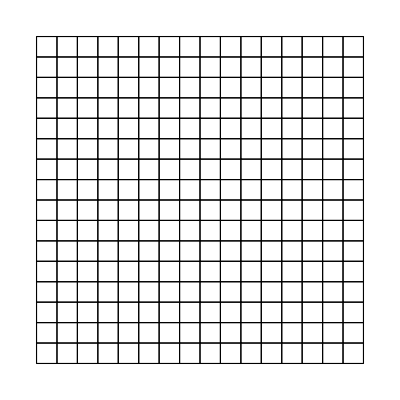

```mathematica
Unprotect[λ,μ,Subscript[ρ, 0],Subscript[ρ, 1],Subscript[ζ, 0],Subscript[ζ, 1],Ω^h,α, αΔT];
ClearAll[λ,μ,Subscript[ρ, 0],Subscript[ρ, 1],Subscript[ζ, 0],Subscript[ζ, 1],Ω^h,α, αΔT];
λ=1; μ=1; 
Subscript[ρ, 0]=0.5;Subscript[ρ, 1]=1.0;
Subscript[ζ, 0]=0.0;Subscript[ζ, 1]=0.5;
L̄=(Subscript[ζ, 1]-Subscript[ζ, 0])/π;
αΔT[ρ_,ζ_]=ρ;
Ω^h=ToElementMesh[Rectangle[{Subscript[ρ, 0],Subscript[ζ, 0]},{Subscript[ρ, 1],Subscript[ζ, 1]}],MaxCellMeasure->0.001,"MeshElementType"->"QuadElement","MeshOrder"->2]
Protect[λ,μ,Subscript[ρ, 0],Subscript[ρ, 1],Subscript[ζ, 0],Subscript[ζ, 1],Ω^h,α,αΔT];
(Ω^h)["Wireframe"]
```

### Create Mesh and Mesh Data Structures

```mathematica
Unprotect[Subscript[n, np],Subscript[n, en],Subscript[n, el],Subscript[n, dof],Subscript[n, guass],Subscript[η, g],Subscript[n, eq],IEN,ID,ElementMesh,NMat];
ClearAll[Subscript[n, np],Subscript[n, en],Subscript[n, el],Subscript[n, dof],Subscript[n, guass],Subscript[η, g],Subscript[n, eq],IEN,ID,(*ElementMesh,*)NMat];
(x⃗)^h=(Ω^h)["Coordinates"];
Subscript[n, np]=Length@((x⃗)^h);
IEN=Apply[List,(Ω^h)["MeshElements"],{1}][[1,1]]ᵀ ;
NMat[ξ_,η_]={(N^(1))[ξ,η],(N^(2))[ξ,η],(N^(3))[ξ,η],(N^(4))[ξ,η],(N^(5))[ξ,η],(N^(6))[ξ,η],(N^(7))[ξ,η],(N^(8))[ξ,η]};
Subscript[n, en]=Dimensions[IEN][[1]];
Subscript[n, el]=Dimensions[IEN][[2]];
Subscript[n, dof]=3;
Subscript[n, guass]=9;
Subscript[η, g]=Subscript[SetUpη, g][(x⃗)^h] ;
ID=SetUpIDArray[];
Subscript[n, eq]=Max[ID];
(Ω^h)["PointElements"]={PointElement[Table[{i},{i,1,Subscript[n, np]}]]};
Protect[Subscript[n, np],Subscript[n, en],Subscript[n, el],Subscript[n, dof],Subscript[n, guass],Subscript[η, g],Subscript[n, eq],IEN,ID,ElementMesh, NMat];
```

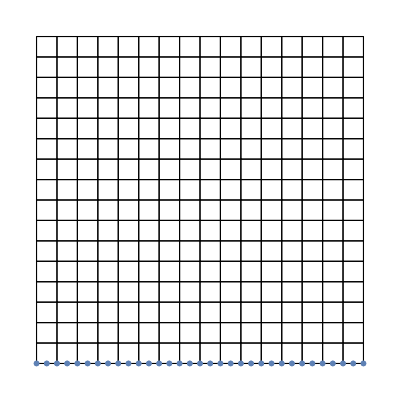

```mathematica
Show[
(Ω^h)["Wireframe"(*["MeshElement" -> "MeshElements","MeshElementIDStyle"->Blue]],
Ω^h["Wireframe"["MeshElement" -> "PointElements","MeshElementIDStyle"->Red]*)],
ListPlot[((x⃗)^h)[[Subscript[η, g][[1]]]],PlotMarkers->{Yellow,Large}],ListPlot[((x⃗)^h)[[Subscript[η, g][[2]]]],PlotMarkers->{Green}],ListPlot[((x⃗)^h)[[Subscript[η, g][[3]]]],PlotMarkers->{\[FreakedSmiley],Large}]]
```

```mathematica
ParallelEvaluate[$KernelID]
DistributeDefinitions[ComputeElementStiffnessMatrix,GuassIntegrate,ElementJacobian,CalculateGuassPoints,IEN,ID,λ,μ,k^e,f^e,NMat,ComputeElementStiffnessMatrixForStressProjection,ComputeGlobalForceMatrix,ComputeGlobalForceMatrixForStressProjection,ComputeGlobalForceMatrixForStressProjection]
Clear[KMat,fMat];
ParallelEvaluate[KMat=SparseArray[{},{Subscript[n, eq],Subscript[n, eq]},0.0];];
ParallelEvaluate[fMat=SparseArray[{},{Subscript[n, eq]},0.0]];
ParallelMap[ComputeElementStiffnessMatrix,Range[Subscript[n, el]]]//AbsoluteTiming
{K1,K2,K3,K4,K5,K6,K7,K8}=ParallelEvaluate[KMat];
KMatP = K1+ K2 + K3+ K4 + K5+ K6 + K7+ K8;
ParallelMap[ComputeGlobalForceMatrix,Range[Subscript[n, el]]]//AbsoluteTiming
{f1,f2,f3,f4,f5,f6,f7,f8}=ParallelEvaluate[fMat];
fMatP = f1+ f2 + f3+ f4 + f5+ f6 + f7+ f8;
t1 = AbsoluteTime[];
sol1=LinearSolve[KMatP,fMatP];
t2 = AbsoluteTime[]-t1
UMat=SplitSolution[sol1];
{Subscript[Un, 1],Subscript[Un, 2],Subscript[Un, 3]}=Table[ElementMeshInterpolation[{Ω^h}, UMat[[i,;;]]//Normal],{i,1,Subscript[n, dof]}];
```

{1,2,3,4,5,6,7,8}

{ComputeElementStiffnessMatrix,ElementJacobian,W,μ,L̄,λ,αΔT,IEN,(x⃗)^h,N_(,ξ)^(1),N_(,ξ)^(2),N_(,ξ)^(3),N_(,ξ)^(4),N_(,ξ)^(5),N_(,ξ)^(6),N_(,ξ)^(7),N_(,ξ)^(8),N_(,η)^(1),N_(,η)^(2),N_(,η)^(3),N_(,η)^(4),N_(,η)^(5),N_(,η)^(6),N_(,η)^(7),N_(,η)^(8),n_en,NMat,n_dof,k^e,GuassIntegrate,CalculateGuassPoints,i,n_guass,Guass,N^(1),N^(2),N^(3),N^(4),N^(5),N^(6),N^(7),N^(8),ID,f^e,ComputeElementStiffnessMatrixForStressProjection,ComputeGlobalForceMatrix,ComputeGlobalForceMatrixForStressProjection}

{36.5722,{{1,8},{2,8},{3,8},{4,8},{5,8},{6,8},{7,8},{8,8},{9,8},{10,8},{11,8},{12,7},{13,7},{14,7},{15,7},{16,7},{17,7},{18,7},{19,7},{20,7},{21,7},{22,7},{23,6},{24,6},{25,6},{26,6},{27,6},{28,6},{29,6},{30,6},{31,6},{32,6},{33,6},{34,5},{35,5},{36,5},{37,5},{38,5},{39,5},{40,5},{41,5},{42,5},{43,5},{44,5},{45,4},{46,4},{47,4},{48,4},{49,4},{50,4},{51,4},{52,4},{53,4},{54,4},{55,4},{56,3},{57,3},{58,3},{59,3},{60,3},{61,3},{62,3},{63,3},{64,3},{65,3},{66,3},{67,2},{68,2},{69,2},{70,2},{71,2},{72,2},{73,2},{74,2},{75,2},{76,2},{77,2},{78,1},{79,1},{80,1},{81,1},{82,1},{83,1},{84,1},{85,1},{86,1},{87,1},{88,1},{89,8},{90,8},{91,8},{92,8},{93,8},{94,8},{95,8},{96,8},{97,8},{98,8},{99,8},{100,3},{101,3},{102,3},{103,3},{104,3},{105,3},{106,3},{107,3},{108,3},{109,3},{110,3},{111,2},{112,2},{113,2},{114,2},{115,2},{116,2},{117,2},{118,2},{119,2},{120,2},{121,2},{122,4},{123,4},{124,4},{125,4},{126,4},{127,4},{128,4},{129,4},{130,4},{131,4},{132,4},{133,6},{134,6},{135,6},{136,6},{137,6},{138,6},{139,6},{140,6},{141,6},{142,6},{143,6},{144,1},{145,1},{146,1},{147,1},{148,1},{149,1},{150,1},{151,1},{152,1},{153,1},{154,1},{155,5},{156,5},{157,5},{158,5},{159,5},{160,5},{161,5},{162,5},{163,5},{164,5},{165,5},{166,8},{167,8},{168,8},{169,8},{170,8},{171,8},{172,8},{173,8},{174,8},{175,8},{176,8},{177,1},{178,1},{179,1},{180,1},{181,1},{182,1},{183,1},{184,1},{185,1},{186,1},{187,3},{188,3},{189,3},{190,3},{191,3},{192,3},{193,3},{194,3},{195,3},{196,3},{197,4},{198,4},{199,4},{200,4},{201,4},{202,4},{203,4},{204,4},{205,4},{206,4},{207,6},{208,6},{209,6},{210,6},{211,6},{212,6},{213,6},{214,6},{215,6},{216,6},{217,5},{218,5},{219,5},{220,5},{221,5},{222,5},{223,5},{224,5},{225,5},{226,5},{227,2},{228,2},{229,2},{230,2},{231,2},{232,2},{233,2},{234,2},{235,2},{236,2},{237,1},{238,1},{239,1},{240,1},{241,1},{242,1},{243,1},{244,1},{245,1},{246,1},{247,3},{248,3},{249,3},{250,3},{251,3},{252,3},{253,3},{254,3},{255,3},{256,3}}}

{1.17765,{{1,8},{2,8},{3,8},{4,8},{5,8},{6,8},{7,8},{8,8},{9,8},{10,8},{11,8},{12,7},{13,7},{14,7},{15,7},{16,7},{17,7},{18,7},{19,7},{20,7},{21,7},{22,7},{23,6},{24,6},{25,6},{26,6},{27,6},{28,6},{29,6},{30,6},{31,6},{32,6},{33,6},{34,5},{35,5},{36,5},{37,5},{38,5},{39,5},{40,5},{41,5},{42,5},{43,5},{44,5},{45,4},{46,4},{47,4},{48,4},{49,4},{50,4},{51,4},{52,4},{53,4},{54,4},{55,4},{56,3},{57,3},{58,3},{59,3},{60,3},{61,3},{62,3},{63,3},{64,3},{65,3},{66,3},{67,2},{68,2},{69,2},{70,2},{71,2},{72,2},{73,2},{74,2},{75,2},{76,2},{77,2},{78,1},{79,1},{80,1},{81,1},{82,1},{83,1},{84,1},{85,1},{86,1},{87,1},{88,1},{89,8},{90,8},{91,8},{92,8},{93,8},{94,8},{95,8},{96,8},{97,8},{98,8},{99,8},{100,4},{101,4},{102,4},{103,4},{104,4},{105,4},{106,4},{107,4},{108,4},{109,4},{110,4},{111,6},{112,6},{113,6},{114,6},{115,6},{116,6},{117,6},{118,6},{119,6},{120,6},{121,6},{122,3},{123,3},{124,3},{125,3},{126,3},{127,3},{128,3},{129,3},{130,3},{131,3},{132,3},{133,7},{134,7},{135,7},{136,7},{137,7},{138,7},{139,7},{140,7},{141,7},{142,7},{143,7},{144,5},{145,5},{146,5},{147,5},{148,5},{149,5},{150,5},{151,5},{152,5},{153,5},{154,5},{155,2},{156,2},{157,2},{158,2},{159,2},{160,2},{161,2},{162,2},{163,2},{164,2},{165,2},{166,4},{167,4},{168,4},{169,4},{170,4},{171,4},{172,4},{173,4},{174,4},{175,4},{176,4},{177,8},{178,8},{179,8},{180,8},{181,8},{182,8},{183,8},{184,8},{185,8},{186,8},{187,3},{188,3},{189,3},{190,3},{191,3},{192,3},{193,3},{194,3},{195,3},{196,3},{197,6},{198,6},{199,6},{200,6},{201,6},{202,6},{203,6},{204,6},{205,6},{206,6},{207,7},{208,7},{209,7},{210,7},{211,7},{212,7},{213,7},{214,7},{215,7},{216,7},{217,5},{218,5},{219,5},{220,5},{221,5},{222,5},{223,5},{224,5},{225,5},{226,5},{227,2},{228,2},{229,2},{230,2},{231,2},{232,2},{233,2},{234,2},{235,2},{236,2},{237,4},{238,4},{239,4},{240,4},{241,4},{242,4},{243,4},{244,4},{245,4},{246,4},{247,8},{248,8},{249,8},{250,8},{251,8},{252,8},{253,8},{254,8},{255,8},{256,8}}}

0.031002

### Post Processing

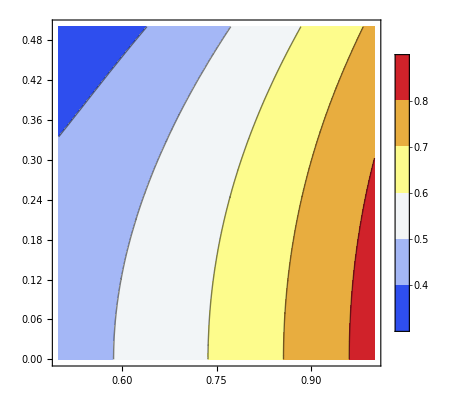

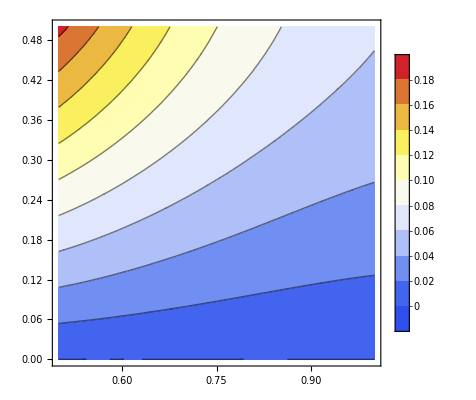

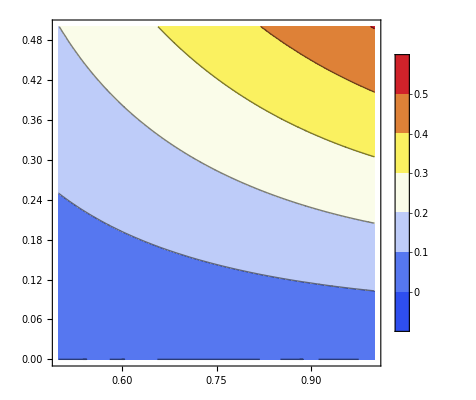

```mathematica
ContourPlot[Subscript[Un, 1][ρ,ζ],{ρ,ζ}∈Ω^h,ColorFunction->"Temperature",AspectRatio->1,PlotLegends->Automatic,PlotRange->All]
ContourPlot[Subscript[Un, 2][ρ,ζ],{ρ,ζ}∈Ω^h,ColorFunction->"Temperature",AspectRatio->1,PlotLegends->Automatic,PlotRange->All]
ContourPlot[Subscript[Un, 3][ρ,ζ],{ρ,ζ}∈Ω^h,ColorFunction->"Temperature",AspectRatio->1,PlotLegends->Automatic,PlotRange->All]
```

### Verify boundary conditions

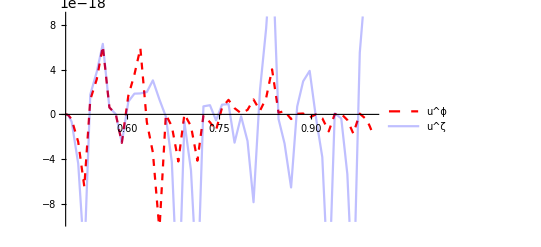

```mathematica
Plot[{Subscript[Un, 2][ρ,Subscript[ζ, 0]],Subscript[Un, 3][ρ,Subscript[ζ, 0]]},{ρ,Subscript[ρ, 0],Subscript[ρ, 1]},PlotStyle->{{Red,Dashed},{Blue,Opacity[0.25]}},PlotLegends->{"u^ϕ","u^ζ"}]
```

### Computing derivatives for u^ρ, u^ϕ , u^ζ w.r.t {ρ, ζ}

```mathematica
ClearAll[aMat,l11Mat,l13Mat,l21Mat,l23Mat,l31Mat,l33Mat];
ParallelEvaluate[aMat=SparseArray[{},{Subscript[n, np],Subscript[n, np]},0.0];];
ParallelEvaluate[l11Mat=l13Mat=l21Mat=l23Mat=l31Mat=l33Mat= SparseArray[{},{Subscript[n, np]},0.0]];
ParallelMap[ComputeElementStiffnessMatrixForStressProjection,Range[Subscript[n, el]]]//AbsoluteTiming
{aP1,aP2,aP3,aP4,aP5,aP6,aP7,aP8}=ParallelEvaluate[aMat];
```

{2.95932,{{Removed[e$40835],8},{Removed[e$40965],8},{Removed[e$41095],8},{Removed[e$41225],8},{Removed[e$41355],8},{Removed[e$41485],8},{Removed[e$41615],8},{Removed[e$41745],8},{Removed[e$41875],8},{Removed[e$42005],8},{Removed[e$42135],8},{Removed[e$14947],7},{Removed[e$15077],7},{Removed[e$15207],7},{Removed[e$15337],7},{Removed[e$15467],7},{Removed[e$15597],7},{Removed[e$15727],7},{Removed[e$15857],7},{Removed[e$15987],7},{Removed[e$16117],7},{Removed[e$16247],7},{Removed[e$39181],6},{Removed[e$39311],6},{Removed[e$39441],6},{Removed[e$39571],6},{Removed[e$39701],6},{Removed[e$39831],6},{Removed[e$39961],6},{Removed[e$40091],6},{Removed[e$40221],6},{Removed[e$40351],6},{Removed[e$40481],6},{Removed[e$39181],5},{Removed[e$39311],5},{Removed[e$39441],5},{Removed[e$39571],5},{Removed[e$39701],5},{Removed[e$39831],5},{Removed[e$39961],5},{Removed[e$40091],5},{Removed[e$40221],5},{Removed[e$40351],5},{Removed[e$40481],5},{Removed[e$39729],4},{Removed[e$39859],4},{Removed[e$39989],4},{Removed[e$40119],4},{Removed[e$40249],4},{Removed[e$40379],4},{Removed[e$40509],4},{Removed[e$40639],4},{Removed[e$40769],4},{Removed[e$40899],4},{Removed[e$41029],4},{Removed[e$50721],3},{Removed[e$50851],3},{Removed[e$50981],3},{Removed[e$51111],3},{Removed[e$51241],3},{Removed[e$51371],3},{Removed[e$51501],3},{Removed[e$51631],3},{Removed[e$51761],3},{Removed[e$51891],3},{Removed[e$52021],3},{Removed[e$39179],2},{Removed[e$39309],2},{Removed[e$39439],2},{Removed[e$39569],2},{Removed[e$39699],2},{Removed[e$39829],2},{Removed[e$39959],2},{Removed[e$40089],2},{Removed[e$40219],2},{Removed[e$40349],2},{Removed[e$40479],2},{Removed[e$49669],1},{Removed[e$49799],1},{Removed[e$49929],1},{Removed[e$50059],1},{Removed[e$50189],1},{Removed[e$50319],1},{Removed[e$50449],1},{Removed[e$50579],1},{Removed[e$50709],1},{Removed[e$50839],1},{Removed[e$50969],1},{Removed[e$40611],6},{Removed[e$40741],6},{Removed[e$40871],6},{Removed[e$41001],6},{Removed[e$41131],6},{Removed[e$41261],6},{Removed[e$41391],6},{Removed[e$41521],6},{Removed[e$41651],6},{Removed[e$41781],6},{Removed[e$41911],6},{Removed[e$16377],7},{Removed[e$16507],7},{Removed[e$16637],7},{Removed[e$16767],7},{Removed[e$16897],7},{Removed[e$17027],7},{Removed[e$17157],7},{Removed[e$17287],7},{Removed[e$17417],7},{Removed[e$17547],7},{Removed[e$17677],7},{Removed[e$41159],4},{Removed[e$41289],4},{Removed[e$41419],4},{Removed[e$41549],4},{Removed[e$41679],4},{Removed[e$41809],4},{Removed[e$41939],4},{Removed[e$42069],4},{Removed[e$42199],4},{Removed[e$42329],4},{Removed[e$42459],4},{Removed[e$40611],5},{Removed[e$40741],5},{Removed[e$40871],5},{Removed[e$41001],5},{Removed[e$41131],5},{Removed[e$41261],5},{Removed[e$41391],5},{Removed[e$41521],5},{Removed[e$41651],5},{Removed[e$41781],5},{Removed[e$41911],5},{Removed[e$52151],3},{Removed[e$52281],3},{Removed[e$52411],3},{Removed[e$52541],3},{Removed[e$52671],3},{Removed[e$52801],3},{Removed[e$52931],3},{Removed[e$53061],3},{Removed[e$53191],3},{Removed[e$53321],3},{Removed[e$53451],3},{Removed[e$42265],8},{Removed[e$42395],8},{Removed[e$42525],8},{Removed[e$42655],8},{Removed[e$42785],8},{Removed[e$42915],8},{Removed[e$43045],8},{Removed[e$43175],8},{Removed[e$43305],8},{Removed[e$43435],8},{Removed[e$43565],8},{Removed[e$51099],1},{Removed[e$51229],1},{Removed[e$51359],1},{Removed[e$51489],1},{Removed[e$51619],1},{Removed[e$51749],1},{Removed[e$51879],1},{Removed[e$52009],1},{Removed[e$52139],1},{Removed[e$52269],1},{Removed[e$52399],1},{Removed[e$17807],7},{Removed[e$17937],7},{Removed[e$18067],7},{Removed[e$18197],7},{Removed[e$18327],7},{Removed[e$18457],7},{Removed[e$18587],7},{Removed[e$18717],7},{Removed[e$18847],7},{Removed[e$18977],7},{Removed[e$19107],7},{Removed[e$42041],6},{Removed[e$42171],6},{Removed[e$42301],6},{Removed[e$42431],6},{Removed[e$42561],6},{Removed[e$42691],6},{Removed[e$42821],6},{Removed[e$42951],6},{Removed[e$43081],6},{Removed[e$43211],6},{Removed[e$42589],4},{Removed[e$42719],4},{Removed[e$42849],4},{Removed[e$42979],4},{Removed[e$43109],4},{Removed[e$43239],4},{Removed[e$43369],4},{Removed[e$43499],4},{Removed[e$43629],4},{Removed[e$43759],4},{Removed[e$42041],5},{Removed[e$42171],5},{Removed[e$42301],5},{Removed[e$42431],5},{Removed[e$42561],5},{Removed[e$42691],5},{Removed[e$42821],5},{Removed[e$42951],5},{Removed[e$43081],5},{Removed[e$43211],5},{Removed[e$53581],3},{Removed[e$53711],3},{Removed[e$53841],3},{Removed[e$53971],3},{Removed[e$54101],3},{Removed[e$54231],3},{Removed[e$54361],3},{Removed[e$54491],3},{Removed[e$54621],3},{Removed[e$54751],3},{Removed[e$43695],8},{Removed[e$43825],8},{Removed[e$43955],8},{Removed[e$44085],8},{Removed[e$44215],8},{Removed[e$44345],8},{Removed[e$44475],8},{Removed[e$44605],8},{Removed[e$44735],8},{Removed[e$44865],8},{Removed[e$52529],1},{Removed[e$52659],1},{Removed[e$52789],1},{Removed[e$52919],1},{Removed[e$53049],1},{Removed[e$53179],1},{Removed[e$53309],1},{Removed[e$53439],1},{Removed[e$53569],1},{Removed[e$53699],1},{Removed[e$40609],2},{Removed[e$40739],2},{Removed[e$40869],2},{Removed[e$40999],2},{Removed[e$41129],2},{Removed[e$41259],2},{Removed[e$41389],2},{Removed[e$41519],2},{Removed[e$41649],2},{Removed[e$41779],2},{Removed[e$19237],7},{Removed[e$19367],7},{Removed[e$19497],7},{Removed[e$19627],7},{Removed[e$19757],7},{Removed[e$19887],7},{Removed[e$20017],7},{Removed[e$20147],7},{Removed[e$20277],7},{Removed[e$20407],7}}}

```mathematica
ParallelMap[ComputeGlobalForceMatrixForStressProjection,Range[Subscript[n, el]]]//AbsoluteTiming
{l11MatP1,l11MatP2,l11MatP3,l11MatP4,l11MatP5,l11MatP6,l11MatP7,l11MatP8}=ParallelEvaluate[l11Mat];
{l13MatP1,l13MatP2,l13MatP3,l13MatP4,l13MatP5,l13MatP6,l13MatP7,l13MatP8}=ParallelEvaluate[l13Mat];
{l21MatP1,l21MatP2,l21MatP3,l21MatP4,l21MatP5,l21MatP6,l21MatP7,l21MatP8}=ParallelEvaluate[l21Mat];
{l23MatP1,l23MatP2,l23MatP3,l23MatP4,l23MatP5,l23MatP6,l23MatP7,l23MatP8}=ParallelEvaluate[l23Mat];
{l31MatP1,l31MatP2,l31MatP3,l31MatP4,l31MatP5,l31MatP6,l31MatP7,l31MatP8}=ParallelEvaluate[l31Mat];
{l33MatP1,l33MatP2,l33MatP3,l33MatP4,l33MatP5,l33MatP6,l33MatP7,l33MatP8}=ParallelEvaluate[l33Mat];
```

{15.4331,{{Removed[e$44995],8},{Removed[e$45765],8},{Removed[e$46535],8},{Removed[e$47305],8},{Removed[e$48075],8},{Removed[e$48845],8},{Removed[e$49615],8},{Removed[e$50385],8},{Removed[e$51155],8},{Removed[e$51925],8},{Removed[e$52695],8},{Removed[e$20537],7},{Removed[e$21307],7},{Removed[e$22077],7},{Removed[e$22847],7},{Removed[e$23617],7},{Removed[e$24387],7},{Removed[e$25157],7},{Removed[e$25927],7},{Removed[e$26697],7},{Removed[e$27467],7},{Removed[e$28237],7},{Removed[e$43341],6},{Removed[e$44111],6},{Removed[e$44881],6},{Removed[e$45651],6},{Removed[e$46421],6},{Removed[e$47191],6},{Removed[e$47961],6},{Removed[e$48731],6},{Removed[e$49501],6},{Removed[e$50271],6},{Removed[e$51041],6},{Removed[e$43341],5},{Removed[e$44111],5},{Removed[e$44881],5},{Removed[e$45651],5},{Removed[e$46421],5},{Removed[e$47191],5},{Removed[e$47961],5},{Removed[e$48731],5},{Removed[e$49501],5},{Removed[e$50271],5},{Removed[e$51041],5},{Removed[e$43889],4},{Removed[e$44659],4},{Removed[e$45429],4},{Removed[e$46199],4},{Removed[e$46969],4},{Removed[e$47739],4},{Removed[e$48509],4},{Removed[e$49279],4},{Removed[e$50049],4},{Removed[e$50819],4},{Removed[e$51589],4},{Removed[e$54881],3},{Removed[e$55651],3},{Removed[e$56421],3},{Removed[e$57191],3},{Removed[e$57961],3},{Removed[e$58731],3},{Removed[e$59501],3},{Removed[e$60271],3},{Removed[e$61041],3},{Removed[e$61811],3},{Removed[e$62581],3},{Removed[e$41909],2},{Removed[e$42679],2},{Removed[e$43449],2},{Removed[e$44219],2},{Removed[e$44989],2},{Removed[e$45759],2},{Removed[e$46529],2},{Removed[e$47299],2},{Removed[e$48069],2},{Removed[e$48839],2},{Removed[e$49609],2},{Removed[e$53829],1},{Removed[e$54599],1},{Removed[e$55369],1},{Removed[e$56139],1},{Removed[e$56909],1},{Removed[e$57679],1},{Removed[e$58449],1},{Removed[e$59219],1},{Removed[e$59989],1},{Removed[e$60759],1},{Removed[e$61529],1},{Removed[e$53465],8},{Removed[e$54235],8},{Removed[e$55005],8},{Removed[e$55775],8},{Removed[e$56545],8},{Removed[e$57315],8},{Removed[e$58085],8},{Removed[e$58855],8},{Removed[e$59625],8},{Removed[e$60395],8},{Removed[e$61165],8},{Removed[e$52359],4},{Removed[e$53129],4},{Removed[e$53899],4},{Removed[e$54669],4},{Removed[e$55439],4},{Removed[e$56209],4},{Removed[e$56979],4},{Removed[e$57749],4},{Removed[e$58519],4},{Removed[e$59289],4},{Removed[e$60059],4},{Removed[e$51811],6},{Removed[e$52581],6},{Removed[e$53351],6},{Removed[e$54121],6},{Removed[e$54891],6},{Removed[e$55661],6},{Removed[e$56431],6},{Removed[e$57201],6},{Removed[e$57971],6},{Removed[e$58741],6},{Removed[e$59511],6},{Removed[e$51811],5},{Removed[e$52581],5},{Removed[e$53351],5},{Removed[e$54121],5},{Removed[e$54891],5},{Removed[e$55661],5},{Removed[e$56431],5},{Removed[e$57201],5},{Removed[e$57971],5},{Removed[e$58741],5},{Removed[e$59511],5},{Removed[e$63351],3},{Removed[e$64121],3},{Removed[e$64891],3},{Removed[e$65661],3},{Removed[e$66431],3},{Removed[e$67201],3},{Removed[e$67971],3},{Removed[e$68741],3},{Removed[e$69511],3},{Removed[e$70281],3},{Removed[e$71051],3},{Removed[e$62299],1},{Removed[e$63069],1},{Removed[e$63839],1},{Removed[e$64609],1},{Removed[e$65379],1},{Removed[e$66149],1},{Removed[e$66919],1},{Removed[e$67689],1},{Removed[e$68459],1},{Removed[e$69229],1},{Removed[e$69999],1},{Removed[e$50379],2},{Removed[e$51149],2},{Removed[e$51919],2},{Removed[e$52689],2},{Removed[e$53459],2},{Removed[e$54229],2},{Removed[e$54999],2},{Removed[e$55769],2},{Removed[e$56539],2},{Removed[e$57309],2},{Removed[e$58079],2},{Removed[e$71821],3},{Removed[e$72591],3},{Removed[e$73361],3},{Removed[e$74131],3},{Removed[e$74901],3},{Removed[e$75671],3},{Removed[e$76441],3},{Removed[e$77211],3},{Removed[e$77981],3},{Removed[e$78751],3},{Removed[e$79521],3},{Removed[e$61935],8},{Removed[e$62705],8},{Removed[e$63475],8},{Removed[e$64245],8},{Removed[e$65015],8},{Removed[e$65785],8},{Removed[e$66555],8},{Removed[e$67325],8},{Removed[e$68095],8},{Removed[e$68865],8},{Removed[e$29007],7},{Removed[e$29777],7},{Removed[e$30547],7},{Removed[e$31317],7},{Removed[e$32087],7},{Removed[e$32857],7},{Removed[e$33627],7},{Removed[e$34397],7},{Removed[e$35167],7},{Removed[e$35937],7},{Removed[e$60281],5},{Removed[e$61051],5},{Removed[e$61821],5},{Removed[e$62591],5},{Removed[e$63361],5},{Removed[e$64131],5},{Removed[e$64901],5},{Removed[e$65671],5},{Removed[e$66441],5},{Removed[e$67211],5},{Removed[e$60829],4},{Removed[e$61599],4},{Removed[e$62369],4},{Removed[e$63139],4},{Removed[e$63909],4},{Removed[e$64679],4},{Removed[e$65449],4},{Removed[e$66219],4},{Removed[e$66989],4},{Removed[e$67759],4},{Removed[e$60281],6},{Removed[e$61051],6},{Removed[e$61821],6},{Removed[e$62591],6},{Removed[e$63361],6},{Removed[e$64131],6},{Removed[e$64901],6},{Removed[e$65671],6},{Removed[e$66441],6},{Removed[e$67211],6},{Removed[e$58849],2},{Removed[e$59619],2},{Removed[e$60389],2},{Removed[e$61159],2},{Removed[e$61929],2},{Removed[e$62699],2},{Removed[e$63469],2},{Removed[e$64239],2},{Removed[e$65009],2},{Removed[e$65779],2},{Removed[e$69635],8},{Removed[e$70405],8},{Removed[e$71175],8},{Removed[e$71945],8},{Removed[e$72715],8},{Removed[e$73485],8},{Removed[e$74255],8},{Removed[e$75025],8},{Removed[e$75795],8},{Removed[e$76565],8},{Removed[e$80291],3},{Removed[e$81061],3},{Removed[e$81831],3},{Removed[e$82601],3},{Removed[e$83371],3},{Removed[e$84141],3},{Removed[e$84911],3},{Removed[e$85681],3},{Removed[e$86451],3},{Removed[e$87221],3}}}

```mathematica
aMatP = aP1+ aP2 + aP3+ aP4 + aP5+ aP6 + aP7+ aP8;
l11MatP = l11MatP1+l11MatP2+l11MatP3+l11MatP4+l11MatP5+l11MatP6+l11MatP7+l11MatP8;
l13MatP = l13MatP1+l13MatP2+l13MatP3+l13MatP4+l13MatP5+l13MatP6+l13MatP7+l13MatP8;
l21MatP = l21MatP1+l21MatP2+l21MatP3+l21MatP4+l21MatP5+l21MatP6+l21MatP7+l21MatP8;
l23MatP = l23MatP1+l23MatP2+l23MatP3+l23MatP4+l23MatP5+l23MatP6+l23MatP7+l23MatP8;
l31MatP = l31MatP1+l31MatP2+l31MatP3+l31MatP4+l31MatP5+l31MatP6+l31MatP7+l31MatP8;
l33MatP = l33MatP1+l33MatP2+l33MatP3+l33MatP4+l33MatP5+l33MatP6+l33MatP7+l33MatP8;
```

```mathematica
ClearAll[sol,U11,U13,U21,U23,U31,U33];
t1 = AbsoluteTime[];
aMatInv=LinearSolve[aMatP];
{U11,U13,U21,U23,U31,U33}=ElementMeshInterpolation[{Ω^h},#] & /@ (aMatInv[#]&/@{l11MatP,l13MatP,l21MatP,l23MatP,l31MatP,l33MatP});
t2 = AbsoluteTime[] - t1
```

0.012001

### Computing Stress and strain

```mathematica
((U⃗)^n)[χ__] := {Subscript[Un, 1]@@χ,Subscript[Un, 2]@@χ,Subscript[Un, 3]@@χ};
X⃗ = {ρ,ϕ,ζ};
Subscript[X⃗, r] = {ρ,ζ};
Subscript[U⃗, n][χ__]:= {g_(1·1·)Subscript[Un, 1]@@χ +g_(1·2·)Subscript[Un, 2]@@χ +g_(1·3·)Subscript[Un, 3]@@χ  ,g_(2·1·)Subscript[Un, 1]@@χ +g_(2·2·)Subscript[Un, 2]@@χ  +g_(2·3·)Subscript[Un, 3]@@χ ,g_(3·1·)Subscript[Un, 1]@@χ +g_(3·2·)Subscript[Un, 2]@@χ  +g_(3·3·)Subscript[Un, 3]@@χ} 
Subscript[γ, n][ρ_,ζ_] =  1/2 Table[D[Subscript[U⃗, n][Subscript[X⃗, r]][[i]],{X⃗[[j]],1}]-  ∑_(k=1)^3 Subscript[U⃗, n][Subscript[X⃗, r]][[k]] Γ_(i·j·)^(k·)+ D[Subscript[U⃗, n][Subscript[X⃗, r]][[j]],{X⃗[[i]],1}]-  ∑_(k=1)^3 Subscript[U⃗, n][Subscript[X⃗, r]][[k]] Γ_(j·i·)^(k·),{i,1,3},{j,1,3}];
(τ^n)[ρ_,ζ_] = Table[∑_(k=1)^3 ∑_(l=1)^3 𝔼^(i·j·k·l·)(Subscript[γ, n][ρ,ζ][[k,l]]-αΔT[ρ,ζ] g_(k·l·)),{i,1,3},{j,1,3}];
```

```mathematica
Symbolize[Subscript[u, ρ,ρ]^h];Symbolize[Subscript[u, ϕ,ρ]^h];Symbolize[Subscript[u, ζ,ρ]^h];
Symbolize[Subscript[u, ρ,ζ]^h]; Symbolize[Subscript[u, ϕ,ζ]^h];Symbolize[Subscript[u, ζ,ζ]^h];  
Symbolize[Subscript[u, h]^(ρ,ρ)];Symbolize[Subscript[u, h]^(ϕ,ρ)];Symbolize[Subscript[u, h]^(ζ,ρ)];
Symbolize[Subscript[u, h]^(ρ,ζ)]; Symbolize[Subscript[u, h]^(ϕ,ζ)];Symbolize[Subscript[u, h]^(ζ,ζ)];  
Symbolize[Subscript[u, ρ]^h];  Symbolize[Subscript[u, ϕ]^h];  Symbolize[Subscript[u, ζ]^h];  
Symbolize[Subscript[u, h]^ρ]; Symbolize[Subscript[u, h]^ϕ] ;Symbolize[Subscript[u, h]^ζ];
```

```mathematica
{(Subscript[u, h]^ρ)[χ__],(Subscript[u, h]^ϕ)[χ__],(Subscript[u, h]^ζ)[χ__]} := {Subscript[Un, 1]@@χ,Subscript[Un, 2]@@χ,Subscript[Un, 3]@@χ};
{(Subscript[u, ρ]^h)[χ__],(Subscript[u, ϕ]^h)[χ__],(Subscript[u, ζ]^h)[χ__]} := {g_(1·1·)Subscript[Un, 1]@@χ +g_(1·2·)Subscript[Un, 2]@@χ +g_(1·3·)Subscript[Un, 3]@@χ  ,g_(2·1·)Subscript[Un, 1]@@χ +g_(2·2·)Subscript[Un, 2]@@χ  +g_(2·3·)Subscript[Un, 3]@@χ ,g_(3·1·)Subscript[Un, 1]@@χ +g_(3·2·)Subscript[Un, 2]@@χ  +g_(3·3·)Subscript[Un, 3]@@χ} ;
{(Subscript[u, h]^(ρ,ρ))[χ__],(Subscript[u, h]^(ϕ,ρ))[χ__],(Subscript[u, h]^(ζ,ρ))[χ__]}:= {U11@@χ,U21@@χ,U31@@χ};
{(Subscript[u, h]^(ρ,ζ))[χ__],(Subscript[u, h]^(ϕ,ζ))[χ__],(Subscript[u, h]^(ζ,ζ))[χ__]}:= {U13@@χ,U23@@χ,U33@@χ};
```

### Given: (∂U^i)/(∂X_j). To Find: (∂U_i)/(∂X_j)? U_i = g_(i k) U^k (∂U_i)/(∂X_j) = (∂g_(i k))/(∂X_j)U^k + g_(i k) (∂U^k)/(∂X_j)

```mathematica
(Subscript[u, ρ,ρ]^h)[ρ_,ζ_]= (∂g_(1·1·))/(∂ ρ)(Subscript[u, h]^ρ)[Subscript[X⃗, r]]+(∂g_(1·2·))/(∂ ρ)(Subscript[u, h]^ϕ)[Subscript[X⃗, r]]+(∂g_(1·3·))/(∂ ρ)(Subscript[u, h]^ζ)[Subscript[X⃗, r]]+ g_(1·1·)(Subscript[u, h]^(ρ,ρ))[Subscript[X⃗, r]] +  g_(1·2·)(Subscript[u, h]^(ϕ,ρ))[Subscript[X⃗, r]]+g_(1·3·)(Subscript[u, h]^(ζ,ρ))[Subscript[X⃗, r]];
(Subscript[u, ϕ,ρ]^h)[ρ_,ζ_]= (∂g_(2·1·))/(∂ ρ)(Subscript[u, h]^ρ)[Subscript[X⃗, r]]+(∂g_(2·2·))/(∂ ρ)(Subscript[u, h]^ϕ)[Subscript[X⃗, r]]+(∂g_(2·3·))/(∂ ρ)(Subscript[u, h]^ζ)[Subscript[X⃗, r]]+ g_(2·1·)(Subscript[u, h]^(ρ,ρ))[Subscript[X⃗, r]] +  g_(2·2·)(Subscript[u, h]^(ϕ,ρ))[Subscript[X⃗, r]]+g_(2·3·)(Subscript[u, h]^(ζ,ρ))[Subscript[X⃗, r]];
(Subscript[u, ζ,ρ]^h)[ρ_,ζ_]= (∂g_(3·1·))/(∂ ρ)(Subscript[u, h]^ρ)[Subscript[X⃗, r]]+(∂g_(3·2·))/(∂ ρ)(Subscript[u, h]^ϕ)[Subscript[X⃗, r]]+(∂g_(3·3·))/(∂ ρ)(Subscript[u, h]^ζ)[Subscript[X⃗, r]]+ g_(3·1·)(Subscript[u, h]^(ρ,ρ))[Subscript[X⃗, r]] +  g_(3·2·)(Subscript[u, h]^(ϕ,ρ))[Subscript[X⃗, r]]+g_(3·3·)(Subscript[u, h]^(ζ,ρ))[Subscript[X⃗, r]];
(Subscript[u, ρ,ζ]^h)[ρ_,ζ_]= (∂g_(1·1·))/(∂ ζ)(Subscript[u, h]^ρ)[Subscript[X⃗, r]]+(∂g_(1·2·))/(∂ ζ)(Subscript[u, h]^ϕ)[Subscript[X⃗, r]]+(∂g_(1·3·))/(∂ ζ)(Subscript[u, h]^ζ)[Subscript[X⃗, r]]+ g_(1·1·)(Subscript[u, h]^(ρ,ζ))[Subscript[X⃗, r]] +  g_(1·2·)(Subscript[u, h]^(ϕ,ζ))[Subscript[X⃗, r]]+g_(1·3·)(Subscript[u, h]^(ζ,ζ))[Subscript[X⃗, r]];
(Subscript[u, ϕ,ζ]^h)[ρ_,ζ_]= (∂g_(2·1·))/(∂ ζ)(Subscript[u, h]^ρ)[Subscript[X⃗, r]]+(∂g_(2·2·))/(∂ ζ)(Subscript[u, h]^ϕ)[Subscript[X⃗, r]]+(∂g_(2·3·))/(∂ ζ)(Subscript[u, h]^ζ)[Subscript[X⃗, r]]+ g_(2·1·)(Subscript[u, h]^(ρ,ζ))[Subscript[X⃗, r]] +  g_(2·2·)(Subscript[u, h]^(ϕ,ζ))[Subscript[X⃗, r]]+g_(2·3·)(Subscript[u, h]^(ζ,ζ))[Subscript[X⃗, r]];
(Subscript[u, ζ,ζ]^h)[ρ_,ζ_]= (∂g_(3·1·))/(∂ ζ)(Subscript[u, h]^ρ)[Subscript[X⃗, r]]+(∂g_(3·2·))/(∂ ζ)(Subscript[u, h]^ϕ)[Subscript[X⃗, r]]+(∂g_(3·3·))/(∂ ζ)(Subscript[u, h]^ζ)[Subscript[X⃗, r]]+ g_(3·1·)(Subscript[u, h]^(ρ,ζ))[Subscript[X⃗, r]] +  g_(3·2·)(Subscript[u, h]^(ϕ,ζ))[Subscript[X⃗, r]]+g_(3·3·)(Subscript[u, h]^(ζ,ζ))[Subscript[X⃗, r]];
```

### U_(i |_j) = (∂U_i)/(∂X_j) - Γ_(i j)^k U_k

```mathematica
CovarDuh[ρ_,ζ_]= {{(Subscript[u, ρ,ρ]^h)[ρ,ζ] -(Γ_(1·1·)^(1·)(Subscript[u, ρ]^h)[{ρ,ζ}]+Γ_(1·1·)^(2·)(Subscript[u, ϕ]^h)[{ρ,ζ}]+ Γ_(1·1·)^(3·)(Subscript[u, ζ]^h)[{ρ,ζ}]),-(Γ_(1·2·)^(1·)(Subscript[u, ρ]^h)[{ρ,ζ}]+Γ_(1·2·)^(2·)(Subscript[u, ϕ]^h)[{ρ,ζ}]+ Γ_(1·2·)^(3·)(Subscript[u, ζ]^h)[{ρ,ζ}]),(Subscript[u, ρ,ζ]^h)[ρ,ζ] -(Γ_(1·3·)^(1·)(Subscript[u, ρ]^h)[{ρ,ζ}]+Γ_(1·3·)^(2·)(Subscript[u, ϕ]^h)[{ρ,ζ}]+ Γ_(1·3·)^(3·)(Subscript[u, ζ]^h)[{ρ,ζ}])},{(Subscript[u, ϕ,ρ]^h)[ρ,ζ] -(Γ_(2·1·)^(1·)(Subscript[u, ρ]^h)[{ρ,ζ}]+Γ_(2·1·)^(2·)(Subscript[u, ϕ]^h)[{ρ,ζ}]+ Γ_(2·1·)^(3·)(Subscript[u, ζ]^h)[{ρ,ζ}]),-(Γ_(2·2·)^(1·)(Subscript[u, ρ]^h)[{ρ,ζ}]+Γ_(2·2·)^(2·)(Subscript[u, ϕ]^h)[{ρ,ζ}]+ Γ_(2·2·)^(3·)(Subscript[u, ζ]^h)[{ρ,ζ}]),(Subscript[u, ϕ,ζ]^h)[ρ,ζ] -(Γ_(2·3·)^(1·)(Subscript[u, ρ]^h)[{ρ,ζ}]+Γ_(2·3·)^(2·)(Subscript[u, ϕ]^h)[{ρ,ζ}]+ Γ_(2·3·)^(3·)(Subscript[u, ζ]^h)[{ρ,ζ}])},{(Subscript[u, ζ,ρ]^h)[ρ,ζ] -(Γ_(3·1·)^(1·)(Subscript[u, ρ]^h)[{ρ,ζ}]+Γ_(3·1·)^(2·)(Subscript[u, ϕ]^h)[{ρ,ζ}]+ Γ_(3·1·)^(3·)(Subscript[u, ζ]^h)[{ρ,ζ}]),-(Γ_(3·2·)^(1·)(Subscript[u, ρ]^h)[{ρ,ζ}]+Γ_(3·2·)^(2·)(Subscript[u, ϕ]^h)[{ρ,ζ}]+ Γ_(3·2·)^(3·)(Subscript[u, ζ]^h)[{ρ,ζ}]),(Subscript[u, ζ,ζ]^h)[ρ,ζ] -(Γ_(3·3·)^(1·)(Subscript[u, ρ]^h)[{ρ,ζ}]+Γ_(3·3·)^(2·)(Subscript[u, ϕ]^h)[{ρ,ζ}]+ Γ_(3·3·)^(3·)(Subscript[u, ζ]^h)[{ρ,ζ}])}};
```

### CovarStrain (γ_(i j)) = 1/2(U_(i |_j) + U_(j |_i)) ContravariantStress (τ^(i j)) = Ε^(i j k l) (γ_(k l) -αΔTg_(k l))

```mathematica
CovarStrain[ρ_,ζ_] = 1/2 Table[CovarDuh[ρ,ζ][[i,j]]+CovarDuh[ρ,ζ][[j,i]],{i,1,3},{j,1,3}];
ContravarStress[ρ_,ζ_] = Table[∑_(k=1)^3 ∑_(l=1)^3 𝔼^(i·j·k·l·)(CovarStrain[ρ,ζ][[k,l]]-αΔT[ρ,ζ] g_(k·l·)),{i,1,3},{j,1,3}];
CovarStress[ρ_,ζ_] =Table[∑_(k=1)^3 ∑_(l=1)^3 ContravarStress[ρ,ζ][[k,l]] g_(i·k·)g_(j·l·),{i,1,3},{j,1,3}];
```

### Compute the total energy

```mathematica
Subscript[Π, en]= NIntegrate[∑_(k=1)^3 ∑_(l=1)^3 ContravarStress[ρ,ζ][[k,l]](CovarStrain[ρ,ζ][[k,l]]-αΔT[ρ,ζ] g_(k·l·))ρ,{ρ,ζ}∈ Ω^h]
```

0.0105756

```mathematica
Π = 0.0;
For[e=1,e≤Subscript[n, el],e++,ComputeEnergy[e]];
Π
```

43.1457

```mathematica
Symbolize[Subscript[σ, ρ]^ρ];Symbolize[Subscript[σ, ϕ]^ρ];Symbolize[Subscript[σ, ζ]^ρ];
Symbolize[Subscript[σ, ρ]^ζ];Symbolize[Subscript[σ, ϕ]^ζ];Symbolize[Subscript[σ, ζ]^ζ];
(Subscript[σ, ρ]^ρ)[ρ_,ζ_] = ∑_(k=1)^3 ContravarStress[ρ,ζ][[k,1]] g_(k·1·);
(Subscript[σ, ϕ]^ρ)[ρ_,ζ_] = ∑_(k=1)^3 ContravarStress[ρ,ζ][[k,1]] g_(k·2·);
(Subscript[σ, ζ]^ρ)[ρ_,ζ_] = ∑_(k=1)^3 ContravarStress[ρ,ζ][[k,1]] g_(k·3·);
(Subscript[σ, ρ]^ζ)[ρ_,ζ_] =∑_(k=1)^3 ContravarStress[ρ,ζ][[k,3]] g_(k·1·);
(Subscript[σ, ϕ]^ζ)[ρ_,ζ_] = ∑_(k=1)^3 ContravarStress[ρ,ζ][[k,3]] g_(k·2·);
(Subscript[σ, ζ]^ζ)[ρ_,ζ_] = ∑_(k=1)^3 ContravarStress[ρ,ζ][[k,3]] g_(k·3·);
```

### Traction free boundary checks

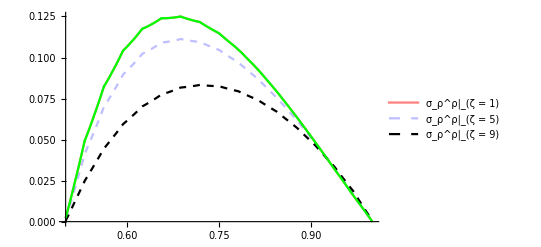

```mathematica
Plot[{(Subscript[σ, ρ]^ρ)[ρ,Subscript[ζ, 1]/5],(Subscript[σ, ρ]^ρ)[ρ,Subscript[ζ, 1]/2],(Subscript[σ, ρ]^ρ)[ρ,Subscript[ζ, 1]/1.2],(τ^n)[ρ,Subscript[ζ, 1]/5][[1,1]]},{ρ,Subscript[ρ, 0],Subscript[ρ, 1]},PlotRange->All,PlotStyle->{{Red,Thickness->0.01,Opacity[0.5]},{Blue,Dashed,Thickness->0.01,Opacity[0.25]},{Black,Dashed,Thickness->0.01},{Green}},PlotLegends->{"σ_ρ^ρ|_(ζ = 1)","σ_ρ^ρ|_(ζ = 5)","σ_ρ^ρ|_(ζ = 9)"}]
```

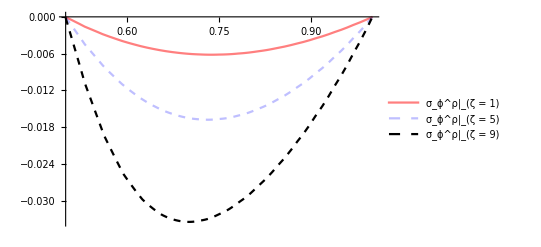

```mathematica
Plot[{(Subscript[σ, ϕ]^ρ)[ρ,Subscript[ζ, 1]/5],(Subscript[σ, ϕ]^ρ)[ρ,Subscript[ζ, 1]/2],(Subscript[σ, ϕ]^ρ)[ρ,Subscript[ζ, 1]/1.2]},{ρ,Subscript[ρ, 0],Subscript[ρ, 1]},PlotRange->All,PlotStyle->{{Red,Thickness->0.01,Opacity[0.5]},{Blue,Dashed,Thickness->0.01,Opacity[0.25]},{Black,Dashed,Thickness->0.01},{Green}},PlotLegends->{"σ_ϕ^ρ|_(ζ = 1)","σ_ϕ^ρ|_(ζ = 5)","σ_ϕ^ρ|_(ζ = 9)"}]
```

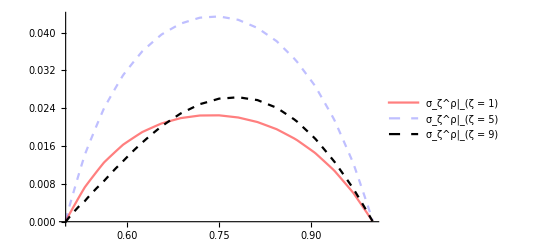

```mathematica
Plot[{(Subscript[σ, ζ]^ρ)[ρ,Subscript[ζ, 1]/5],(Subscript[σ, ζ]^ρ)[ρ,Subscript[ζ, 1]/2],(Subscript[σ, ζ]^ρ)[ρ,Subscript[ζ, 1]/1.2]},{ρ,Subscript[ρ, 0],Subscript[ρ, 1]},PlotRange->All,PlotStyle->{{Red,Thickness->0.01,Opacity[0.5]},{Blue,Dashed,Thickness->0.01,Opacity[0.25]},{Black,Dashed,Thickness->0.01},{Green}},PlotLegends->{"σ_ζ^ρ|_(ζ = 1)","σ_ζ^ρ|_(ζ = 5)","σ_ζ^ρ|_(ζ = 9)"}]
```

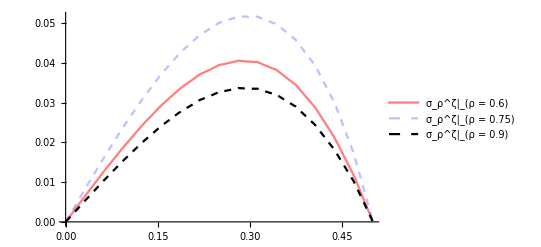

```mathematica
Plot[{(Subscript[σ, ρ]^ζ)[0.6,ζ],(Subscript[σ, ρ]^ζ)[0.75,ζ],(Subscript[σ, ρ]^ζ)[0.9,ζ]},{ζ,Subscript[ζ, 0],Subscript[ζ, 1]},PlotRange->All,PlotStyle->{{Red,Thickness->0.01,Opacity[0.5]},{Blue,Dashed,Thickness->0.01,Opacity[0.25]},{Black,Dashed,Thickness->0.01},{Green}},PlotLegends->{"σ_ρ^ζ|_(ρ = 0.6)","σ_ρ^ζ|_(ρ = 0.75)","σ_ρ^ζ|_(ρ = 0.9)"}]
```

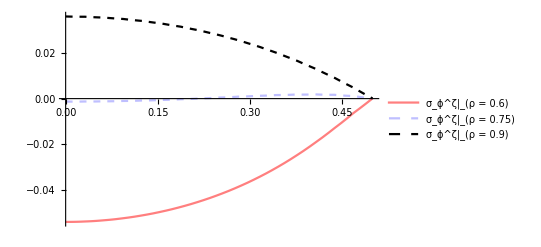

```mathematica
Plot[{(Subscript[σ, ϕ]^ζ)[0.6,ζ],(Subscript[σ, ϕ]^ζ)[0.75,ζ],(Subscript[σ, ϕ]^ζ)[0.9,ζ]},{ζ,Subscript[ζ, 0],Subscript[ζ, 1]},PlotRange->All,PlotStyle->{{Red,Thickness->0.01,Opacity[0.5]},{Blue,Dashed,Thickness->0.01,Opacity[0.25]},{Black,Dashed,Thickness->0.01},{Green}},PlotLegends->{"σ_ϕ^ζ|_(ρ = 0.6)","σ_ϕ^ζ|_(ρ = 0.75)","σ_ϕ^ζ|_(ρ = 0.9)"}]
```

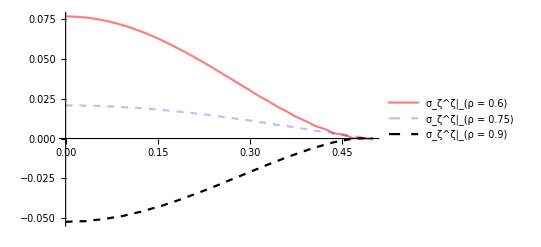

```mathematica
Plot[{(Subscript[σ, ζ]^ζ)[0.6,ζ],(Subscript[σ, ζ]^ζ)[0.75,ζ],(Subscript[σ, ζ]^ζ)[0.9,ζ]},{ζ,Subscript[ζ, 0],Subscript[ζ, 1]},PlotRange->All,PlotStyle->{{Red,Thickness->0.01,Opacity[0.5]},{Blue,Dashed,Thickness->0.01,Opacity[0.25]},{Black,Dashed,Thickness->0.01},{Green}},PlotLegends->{"σ_ζ^ζ|_(ρ = 0.6)","σ_ζ^ζ|_(ρ = 0.75)","σ_ζ^ζ|_(ρ = 0.9)"}]
```